DateLong

# 1D Model Experiments

## Plots for dissertation

Jan-Hendrik Prinz

DFG Research Center Matheon, FU Berlin, Arnimallee 6, 14195 Berlin, Germany

jan-hendrik.prinz@fu-berlin.de

## Section.INITIALIZATION

[ All files and function to be initialized at startup ]

### Basic Packages

[ Here are the main packeges for every project ]

```mathematica
<<ProjectManagement/ProjectManagement.m
<<BibTeX/BibTeX.m
<<NetCDFReader/NetCDFReader.m
<<PaperStyle/PaperStyle.m
```

[ If the packages are not installed, run this little program, this will load the packages from the package folder ! ]

```mathematica
Module[{packagesToBeLoaded,result, $projectNameSelected,$basePath,$packagesPath},
$projectNameSelected=NotebookFileName[];
$basePath=FileNameTake[$projectNameSelected,{1,-2}];
$packagesPath = FileNameJoin[{$basePath,"packages"}];
If[FileExistsQ[$packagesPath],
packagesToBeLoaded = FileNames["*.m*",$packagesPath];
result=Map[Print["Load package : "<>FileNameTake[#]];Get[#];&, packagesToBeLoaded];
]
]
```

### InitializeProject

[ Create a project and put everything in a folder. If already done, just get the appropriate path variables ]

```mathematica
InitializeProject[];
```

### Additional Packages

[ Here go all additional packages to be loaded on startup ]

```mathematica
<<MSM`
```

### Path settings

[ System specific paths and files set ]

```mathematica
$DefaultBibTeXLibrary="/Users/jan-hendrikprinz/Studium/Literature/bibtex/complete.bib";
```

### Project Management

```mathematica
ExportProject[]
```

```mathematica
ProjectSaveBackUp[]
```

## Section.RATE-THEORY PAPER

### Initialize

### Functions

#### Discretization Functions

```mathematica
MakeEqualDataBinning[data_,num_]:=Module[{str,length,width,pp,mp,cp},
str=Sort[data];
length=Length[data];
width=length/num;
pp=Table[{Round[nn],Round[nn]+1},{nn,width,length-width,width}];
mp=Map[Mean[str[[#]]]&,pp];
cp=Map[Mean,Transpose[{Drop[mp,1],Drop[mp,-1]}]];
Join[{2mp[[1]]-cp[[1]]},cp,{2mp[[-1]]-cp[[-1]]}]
]
```

```mathematica
MakeStrechedBinning[data_,num_,fac_]:=Module[
{str,sk,fnc,norm,tf,ctf,ctfi,ictf},
str=Sort[data];
sk=SmoothKernelDistribution[str];
fnc=(PDF[sk,y])^(1/fac);
norm=NIntegrate[fnc,{y,str[[1]],str[[-1]]}];
tf=FunctionInterpolation[1/norm*fnc,{y,str[[1]],str[[-1]]},InterpolationPoints->200];
ctf[y_]:=Integrate[tf[x],{x,str[[1]],y}];
ctfi=FunctionInterpolation[ctf[y],{y,str[[1]],str[[-1]]},InterpolationPoints->200];
ictf[y_]:=x/.FindMinimum[{(ctfi[x]-y)^2,{str[[1]]≤x≤str[[-1]]}},{x,0.5}][[2]];
Table[(ictf[y]),{y,0.5/num,1,1./num}]
]
```

```mathematica
MakePaddedBinning[data_,num_,pad_]:=Module[
{str,length,width, removePoints,miP,maP,mi,ma},
str=Sort[data];
length=Length[data];
width=length/num;
removePoints=Ceiling[length*pad/2];
miP=str[[1+removePoints]];
maP=str[[length-removePoints]];
mi=str[[1]];
ma=str[[-1]];
(Range[0,num+1]-0.5)*(maP-miP)/num+miP
]
```

```mathematica
MakeEqualWidthBinning[data_,num_]:=Module[
{str,length,width,mi,ma},
str=Sort[data];
length=Length[data];
width=length/num;
mi=str[[1]];
ma=str[[-1]];
(Range[1,num]-0.5)*(ma-mi)/num+mi
]
```

```mathematica
$DefaultDiscretizationPoints={0.0};
$DefaultNumberOfDiscreteStates=50;
```

```mathematica
GetDiscretization[v_?VectorQ,MDopts___]:=Module[
{centerMode},
centerMode=Centers/.{MDopts}/.{Centers->"Width"};
{mi,ma}={Min[v],Max[v]};
centers=Switch[
centerMode,
"Fixed",
$DefaultDiscretizationPoints,
"Width",
MakeEqualWidthBinning[v,$DefaultNumberOfDiscreteStates],
{"Width",_?IntegerQ},
MakeEqualWidthBinning[v,centerMode[[2]]],
"Mass",
MakeEqualDataBinning[v,$DefaultNumberOfDiscreteStates],
{"Mass",_?IntegerQ},
MakeEqualDataBinning[v,centerMode[[2]]],
"Stretched",
MakeStrechedBinning[v,$DefaultNumberOfDiscreteStates,3],
{"Stretched",_?IntegerQ,_?IntegerQ},
MakeStrechedBinning[v,centerMode[[2]],centerMode[[3]]],
"Padded",
MakePaddedBinning[v,$DefaultNumberOfDiscreteStates,0.001],
{"Padded",_?IntegerQ,_?NumberQ},
MakePaddedBinning[v,centerMode[[2]],centerMode[[3]]],
_,
$DefaultDiscretizationPoints
];
weight=(Drop[#,1]-Drop[#,-1])&[Join[{mi},Map[Mean,Transpose[{Drop[centers,1],Drop[centers,-1]}]],{ma}]];
Discretization[
"Centers"->centers,
"Mode"->centerMode,
"Min"->mi,
"Max"->ma,
"States"->Length[centers],
"Weight"->weight
]
]
```

```mathematica
Discretization/:Use[Discretization[opts___]]:=Module[
{},
Function[
data,
centers=("Centers"/.{opts});
length=Length[data];
nf=Nearest[centers->Automatic];
states="States"/.{opts};
discretized=Map[First[nf[#]]&,data];
all=Range[states];
usedCenterID=Union[discretized];
void=Complement[all,usedCenterID];
count=Sort[Join[Tally[discretized],Thread[{void,0}]],#1[[1]]<#2[[1]]&];
weight="Weight"/.{opts};
density=#/Total[#]&[1.0*count[[All,2]]/length/weight];
TimeSeries[
discretized,
"Length"->length,
"Discretization"-> Discretization[opts],
"Used"->usedCenterID,
"Void"->void,
"All"->all,
"Clustering"->RemoveClusterMatrix[void,states],
"Counts"->count[[All,1]],
"BinSize"->weight,
"Density"->Transpose[{centers,density}]
]
]
]
```

```mathematica
Discretization/:MakeBoxes[Discretization[opts___],StandardForm]:=InterpretationBox[#,Estimation[opts]]&[RowBox[{"𝔻","[","Min"/.List[opts],",","Max"/.List[opts],"]","→","{","States"/.List[opts],"}"}]]
```

```mathematica
Estimation/:MakeBoxes[Estimation[opts___],StandardForm]:=InterpretationBox[#,Estimation[opts]]&[RowBox[{"𝔼","[",Length["Projection"/.List[opts]],",","States"/.List[opts],"]","→",ToString["TimeScales"/.List[opts]]}]]
```

#### General Settings

```mathematica
Off[OptionValue::nodef]
```

#### Plot Functions

#### Mathemathical Helper Functions

#### General Helper Functions

```mathematica
Op[s_:Null]:=Function[x,
If[
s=!=Null,
s/.Select[List@@x,!ListQ[#]&],
Select[List@@x,!ListQ[#]&]
]]
```

```mathematica
PadInteger[int_,digits_]:=StringTake["00000000"<>ToString[int],-digits]
```

### Run Trajectories / Read Data

#### Settings

There are two calibrated fibers in the dataset from John, no #1 and no #6.

```mathematica
$DefaultPathToTrajectories="/Users/jan-hendrikprinz/Studium/Daten/elms-apoMB/calibrated/";
```

```mathematica
$ListOfApoTraceFileNames=
{
"no1"->$DefaultPathToTrajectories<>"fiber1.mat",
"no6"->$DefaultPathToTrajectories<>"fiber6.mat"
};
```

#### Functions

```mathematica
LoadApoTraces[]:=Module[{name},
listOfApoTraces=Map[
#[[1]]-> Import[#[[2]]][[1,All,1,All,1]]&,$ListOfApoTraceFileNames];
]
```

```mathematica
LoadApoTraces[];
```

```mathematica
SetTraceApo[traceID_,mvWindow_]:=Module[{},
pullingData=TimeSeries[-apotraces[[traceID]]];
pullingData=TimeSeries[MovingAverage[pullingData[[1]],mvWindow]];
]
```

```mathematica
GetTraceApo[fiberName_,traceID_,mvWindow_:1]:=
Module[{},
apotraces=fiberName/.listOfApoTraces;
pullingData=-apotraces[[traceID]];
pullingData=MovingAverage[pullingData,mvWindow];
pullingData
]
```

```mathematica
GetAllTraces[fiberName_]:=Module[
{},
apotraces=fiberName/.listOfApoTraces
]
```

### Example

```mathematica
trace=GetTraceApo["no1",10];
```

```mathematica
disc=GetDiscretization[trace,Centers->{"Width",20}];
```

```mathematica
ts1=Use[disc][trace]
```

𝕊_20[1]→⟨3000000⟩

```mathematica
Op["Density"][ts1][[All,2]]
%//Total
```

```mathematica
Op[][disc]
```

{Centers→{2.66966,2.82385,2.97803,3.13222,3.28641,3.44059,3.59478,3.74897,3.90315,4.05734,4.21153,4.36571,4.5199,4.67409,4.82827,4.98246,5.13665,5.29084,5.44502,5.59921},Mode→{Width,20},Min→2.59257,Max→5.6763,States→20,Weight→{0.154187,0.154187,0.154187,0.154187,0.154187,0.154187,0.154187,0.154187,0.154187,0.154187,0.154187,0.154187,0.154187,0.154187,0.154187,0.154187,0.154187,0.154187,0.154187,0.154187}}

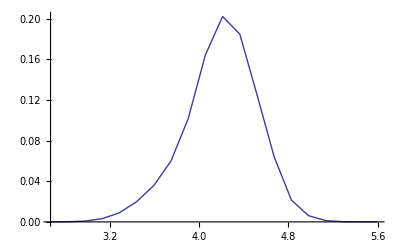

```mathematica
ListPlot[Op["Density"][ts1],Joined->True]
```

#### Execution

Set default to 20 states

```mathematica
$DefaultNumberOfDiscreteStates=20;
```

### System specific

Create Clustering that clusters left and rightmost states together. Useful for Gaussian-like distributions.

```mathematica
clM=CrispClusterMatrix[{Range[1,4],Apply[Sequence,Partition[Range[5,16],1]],Range[17,20]}];
```

### Generate Correlation Matrices

#### Function

LagtimePadding is the lagtime cut of to ensure the same number of counts for different lagtimes and is this the maximal lagtime possible.

```mathematica
$DefaultRangeOfTimeScales=Range[1,500];
$DefaultLagtimePadding=1000;
```

```mathematica
TimeSeries/:ToListOfCorrelations[TimeSeries[ts_,opts___],CLopts___]:=Module[
{listOfCM},
range="Range"/.{CLopts}/.{"Range"->$DefaultRangeOfTimeScales};
padding="LagtimePadding"/.{CLopts}/.{"LagtimePadding"->$DefaultLagtimePadding};
reversible="Reversible"/.{CLopts}/.{"Reversible"->False};
If[padding>0,
listOfCM=Map[ToCountMatrix[TimeSeries[Take[ts,{1,Length[ts]-padding+#}]],Lagtime->#,Reversible->reversible]&,range],
listOfCM=Map[ToCountMatrix[TimeSeries[ts],Lagtime->#,Reversible->reversible]&,range]
]
]
```

### Check consitency of traces

```mathematica
listOfTS=Table[
Table[
disc=GetDiscretization[trace,Centers->{"Width",20}];
ts=Use[disc][trace]
,{trace,GetAllTraces[fiber][[All]]}
]
,{fiber,{"no1","no6"}}
];
```

```mathematica
listOfListOfCM=Table[
Table[
ToListOfCorrelations[ts]
,{ts,fiber}
]
,{fiber,listOfTS}
];
```

```mathematica
listOfTS=Import[ToResourceFile["listOfTimeSeries.m"]];
listOfListOfCM=Import[ToResourceFile["listOfCorrelations.m"]];
```

```mathematica
SetSIMFull[nn_]:=Module[{},
{no,listOfCM,evdITS,cmA,cmB,itsEst}=allERG[[nn]];
disc=allTrajDisc[[nn]];
hist=Transpose[{disc, Map[Total,listOfCM[[1,1]]]}];
]
```

```mathematica
GetSIMSimple[nn_]:=Module[{},
no=nn;
SetTraceApo[no,1];
discTS1D= wok[pullingData[[1]],20];
discTS=TimeSeries[discTS1D[[1]]];
listOfCM=Map[ToCountMatrix[TimeSeries[Take[discTS[[1]],{1,Length[discTS]-1000+#}]],Lagtime->#,Reversible->False]&,Range[1,500,1]];
hist=Map[Total,listOfCM[[1,1]]];
{
"Correlations"->listOfCM,
"Centers"->"Centers"/.discTS1D[[4]],
"Histogram"->hist
}
]
```

```mathematica
SetSIM[nn_]:=Module[{},
no=nn;
listOfCM="Correlations"/.allERG2[[nn]];
disc="Centers"/.allERG2[[nn]];
hist="Histogram"/.allERG2[[nn]];
]
```

```mathematica
allERG2=
Table[
GetSIMSimple[no]
,{no,1,Length[apotraces]}
];
histList="Histogram"/.allERG2;
discList="Centers"/.allERG2
```

```mathematica
Show[
Graphics[{Table[
SetSIM[nn];
Inset[ListPlot[Transpose[{disc,hist}],Filling->{1->{Bottom,Directive[Gray,Opacity[0.2]]}},Frame->False,Axes->True,AxesOrigin->{0,0},Ticks->None,FrameTicks->None,PlotRange->{{2.4,7.2},{0,1000000}}],{nn,nn}*3,Center,100,{{0.7,-0.3},{0,1}}],
{nn,1,Length[apotraces]}
]
}]
,Frame->False,ImageSize->640,PlotRange->{{-10,10},{-10,10}}*10]
```

```mathematica
ev2List=Table[
SetSIM[nn];
Transpose[{disc[[Range[4,17]]],hist[[Range[4,17],2]]*itsEst[[100,6,2,2]]}],
{nn,1,Length[apotraces]}
];
```

```mathematica
svdAllList=Table[
SetSIM[nn];
svdList=Map[SingularValueDecomposition[(ToCorrelationMatrix@#)[[1]]]&,listOfCM]
,{nn,1,Length[apotraces]}];
```

```mathematica
Manipulate[
svdList=svdAllList[[nn]];
ListLogPlot[Transpose[Map[Diagonal,svdList[[Range[1,500],2]]]][[{1,2,3,4,5,6}]],Epilog->{Dashed,Opacity[0.2],Rectangle[{0,Log[0.0001]},{500,Log[0.001]}]},PlotRange->{0.0002,0.5},ImageSize->480],
{nn,1,Length[apotraces],1}
]
```

{a11→0.0541529,a12→0.00113645,a21→0.079385,a22→0.00881304,b1→6.10955×10^-6,b2→0.0055477}

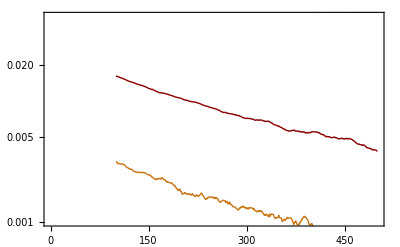

```mathematica
no=11;
pF=Identity;
rrange=Range[100,500];

model=pF[a11*Exp[-t*b1]+a12*Exp[-t*b2]*s+(1-s)*a21*Exp[-t*b1]+a22*Exp[-t*b2]];
dn=Table[
Transpose[{rrange,pF@(Transpose[Map[Diagonal,svdAllList[[no,rrange,2]]]][[nn]])}],
{nn,1,3}
];
lag=dn[[1,All,1]];
v1=dn[[1,All,2]];
v2=dn[[2,All,2]];
v3=dn[[3,All,2]];
data=Join[Transpose[{lag,0*lag,v1}],Transpose[{lag,0*lag+1,v2}],Transpose[{lag,0*lag+2,v3}]];
res=FindFit[data,model,{{a11,0.1},{a12,0.01},{a21,0.01},{a22,0.1},{b1,1/2000},{b2,1/200}},{t,s}]
Show[{
ListLogPlot[dn],
LogPlot[{model/.res/.s->0,model/.res/.s->1},{t,0,500}]
},PlotRange->{{0,500},Log@{0.001,0.05}}]
```

```mathematica
res=FindFit[Transpose[{Range[100,500],Log@(Transpose[Map[Diagonal,svdAllList[[1,Range[100,500],2]]]][[2]])}],a x+b,{a,b},x];
1/a/.res
```

-3296.62

### Spectral Fitting

#### Helper Functions

```mathematica
VV[var_,st_?ListQ,opts___]:=Module[{size},size=Padding/.{opts}/.{Padding->2};
ToExpression[ToString[var]<>StringJoin[Map[PadInteger[#,size]&,st]]]]
```

```mathematica
selModel[ii_,jj_]:=Thread[Flatten@sM->UnitVector[size^2,(ii-1)*size+jj]]
```

```mathematica
GetSingularValues[listOfCM_]:=Module[{},
Map[Diagonal[SingularValueDecomposition[(ToCorrelationMatrix@#)[[1]]][[2]]]&,listOfCM]
]
```

```mathematica
GetTransitionEigenvalues[listOfCM_]:=Module[{},
Map[Eigenvalues[((ToCorrelationMatrix@#))[[1]]]&,listOfCM]
]
```

```mathematica
GetCorrelationEigenvalues[listOfCM_]:=Module[{},
Map[Eigenvalues[(ToTransitionMatrix@(ToCorrelationMatrix@#))[[1]]]&,listOfCM]
]
```

```mathematica
Worm[data_,scale_:{0.000001,1},shift_:{0,0},extend_:-1]:=Module[
{
},
points=Map[Reverse[#*scale]&,data];
Polygon@Join[Map[#+shift&,points],Map[#*{extend,1}+shift&,Reverse@points]]
]
```

#### Functions

```mathematica
MakeAnalyticPlots[Estimation[results___]]:=
Module[{},
svdLine="SVD"/.List@results;
pro="Projection"/.List@results;
qMatEst="QMatrix"/.List@results;
size="States"/.List@results;
trange="FittedTimeScales"/.List@results;
result="EstimationResult"/.List@results;
corMList="Correlations"/.List@results;
timescales="TimeScales"/.List@results;
Print@Grid[{{
ListLogPlot[svdLine[[{1,2,3,4,5}]],
Prolog->{Dashed,Opacity[0.15],
Rectangle[{-50,Log[0.0001]},{550,Log[threshold]}],
Rectangle[{trange[[1]],Log[0.0001]},{trange[[-1]],Log[0.5]}],
Black,Opacity[1],Dashed,
Line[{{svdTime,Log[0.0001]},{svdTime,Log[0.5]}}]
},
Filling->Table[nn->{0.0001,Directive[Blend[{$Colors[[nn]],White},0.8]]},{nn,5,5}],
PlotRange->{0.0002,0.5},
ImageSize->360,
FrameLabel->{"Lagtime τ","SVD"},
ImagePadding->{{70,1},{50,1}}
],
ListPlot[
Transpose[pro.qMatEst],
PlotRange->All,
ImageSize->360,
Filling->Table[nn->{0,Directive[$Colors[[nn]],Opacity[0.2]]},{nn,1,size}],
GridLines->{None,{0}},
FrameLabel->{"State","Non-orthogonal GEVD"},
Epilog->{Red,Table[
Text[Row[{Subscript["t",ToString[nn]]," = ",Style[ToString[timescales[[nn-1]]],FontColor->$Colors[[nn]]]}],Scaled[{0.85,0.10+0.07*(size-nn)}]],
{nn,2,size}]
},
ImagePadding->{{70,1},{50,1}}
],
ListPlot[
Transpose[pro],
PlotRange->All,
ImageSize->360,
FrameLabel->{"State","Singular Vectors"},
ImagePadding->{{70,1},{50,1}}
]
}}
];
showCurvature=If[True,1,0];
Print@Grid[
Table[
Show[
{
mean=Mean[corMList[[trange,i,j]]];
mFunc=model/.selModel[i,j]/.result;
ergList=Map[(mFunc/.{t->#})-mean&,trange];
ListPlot[
Transpose[{Range[1,500],Range[1,500]*0}],
PlotRange->All,
PlotStyle->ToPlotStyle[{1},{Directive[Dashed, Thickness[Medium]]}],PlotRangePadding->Scaled[0.05],ImageSize->240,PlotRange->All
],
Plot[{showCurvature*(mFunc-mean),showCurvature*(mFunc-mean)},{t,trange[[1]],trange[[-1]]},
PlotStyle->{Directive[{Thickness[0.05],Opacity[0.4],Red}],Directive[{Thickness[0.03],Opacity[0.8],White}]},PlotRange->All
],
ListPlot[
Transpose[{trange,corMList[[trange,i,j]]-mean-(1-showCurvature)*ergList}],
Epilog->{Dashed,Thick,Line[{{1,0},{500,0}}]},PlotRange->All,
PlotStyle->ToPlotStyle[{1},{Directive[Dotted]}],PlotRangePadding->Scaled[0.05],ImageSize->240,PlotRange->All
]
},
PlotRange->{{1,500},If[False,{-0.05,1.05},{-0.1,0.1}*0.05]},FrameTicks->None,ImagePadding->{{If[j==1,50,0],0},{If[i==1,50,0],0}}+1,
ImageSize->{240+If[j==1,50,0],150+If[i==1,50,0]},
PlotRangeClipping->True,FrameLabel->{"SVD "<>ToString[j],"SVD "<>ToString[i]}
]
,{i,size,1,-1},{j,size}
]
,Spacings->{0.01,0.01}
];
]
```

```mathematica
SpectralFitting[listOfCM_,opts___]:=
Module[{},
threshold=Threshold/.{opts}/.{Threshold->0.0005};
trange=TimeRange/.{opts}/.{TimeRange->Range[150,500]};
svdTime=SVDTime/.{opts}/.{SVDTime->150};
svdLine=Transpose[GetSingularValues[listOfCM]];
statesT=Length@Select[Map[Mean,svdLine[[All,trange]]],#>threshold&];
states=States/.{opts}/.{States->3,Threshold->statesT};
lI=InitialTS/.{opts}/.{InitialTS->{1/1000,1/200,1/50,1/5000,1/500}};
lI=lI[[Range[states-1]]];
rrange=Range[states];
ergEVD=Drop[ToImpliedTimescales[((Spectrum@MaximumLikelihoodMatrix@Last@listOfCM)[[Range[states]]]),Lagtime@Last@listOfCM],1];
pro=SingularValueDecomposition[(ToCorrelationMatrix@(listOfCM[[svdTime]]))[[1]]][[1,All,rrange]];
proI=SingularValueDecomposition[(ToCorrelationMatrix@(listOfCM[[svdTime]]))[[1]]][[1,rrange]];
qM=Table[VV[q,{i,j}],{i,rrange},{j,states}];
lV=Table[VV[l,{i}],{i,states-1}];
lD=DiagonalMatrix[Join[{1},Exp[-t*lV]]];
sM=Table[VV[s,{i,j}],{i,rrange},{j,rrange}];
model=Total@Flatten[sM*qM.lD.Transpose@qM];
constraints=Thread[lV≥0];
corMList=Map[Chop[Transpose[pro].(ToCorrelationMatrix@#)[[1]].pro]&,listOfCM];
data=Flatten[Table[Transpose[Join[{trange},Transpose[{UnitVector[states^2,(i-1)*states+j]}].{trange*0+1},{corMList[[trange,rrange[[i]],rrange[[j]]]]}]],{i,states},{j,states}],2];
data//Dimensions;
vars=Join[{t},Flatten[sM]];
params=Join[Flatten[Transpose[{qM,IdentityMatrix[states]},{3,1,2}],{1,2}],Flatten[Transpose[{lV,lI}],{1}]];
useConstraints=UseConstraints/.{opts}/.{UseConstraints->False};
If[useConstraints,
result=FindFit[data,{model,constraints},params,vars,MaxIterations->2000];
,
result=FindFit[data,model,params,vars,MaxIterations->2000];
];
qMatEst=qM/.result;
timescales=1/lV/.result;
modelParam=(model-val)/.result;
varsA=Join[vars,{val}];
residual=(Norm@Map[modelParam/.Thread[varsA-> #]&,data])^2;
Estimation[
"TimeScales"->timescales,
"Eigenvalues"->Exp[-1/timescales],
"QMatrix"->qMatEst,
"EstimationResult"->result,
"SVD"->svdLine[[Range[5]]],
"Projection"->pro,
"Rejection"->proI,
"FittedTimeScales"->trange,
"States"->states,
"Residual"->residual,
"Correlations"->corMList,
"EVDTimeScales"-> ergEVD,
"EVDEigenvalues"-> Exp[-1/ergEVD]
]
]
```

```mathematica
RegularizeLeftEV[leftEV_,opts___]:=Module[{},
cf=CufOffFunction/.{opts}/.CufOffFunction->Function[x,If[Abs[x]<0.004,x/0.004,Sign[x]]];
mPiI=Inverse[DiagonalMatrix[leftEV[[1]]]]/Sign[Mean[leftEV[[1]]]];
mW=mPiI.Transpose[leftEV];
length=Length[leftEV[[1]]];
piF=Interpolation[(leftEV)[[1]]];
piF=Interpolation[(Map[cf,leftEV,{2}])[[1]]];
vTilde=Table[
gg=Interpolation[(Transpose@mW)[[ev]]];
hh[y_]:=(D[gg[x],x])/.x->y;
ppos=Round[length/2];
jj[z_]:=Sign[piF[ppos]]*gg[ppos]+NIntegrate[piF[y]hh[y],{y,ppos,z},PrecisionGoal->5,AccuracyGoal->5];
ffFix=Interpolation[Table[{nn,jj[nn]},{nn,1,length,0.2}]];
vec=Table[ffFix[x],{x,1,length}]
,
{ev,1,Length[leftEV]}
]
]
```

```mathematica
EnhancedPCCA[evecR_,opts___]:=
Module[{},
(* 
	Specify way to regularize right eigenvectors 
	1. Use flattened Right EVS
	2. Dont do anything
	3. Use only finite set of all possible microstates for estimation
*)

maxIter=MaxIterations/.{opts}/.{MaxIterations->500};
states=States/.{opts}/.{States->Length[evecR]};

alpha=Table[VV[a,{i,j}],{i,states},{j,states}];
Table[alpha[[1,i]]=-Total[Drop[alpha[[All,i]],1]];,{i,1,states}];
alpha[[1,1]]+=1.0;

vTilde=evecR[[Range[states]]];
constraints=Flatten@Map[Thread,Thread[alpha.vTilde>0]];
minimizer=Chop[Total@Diagonal@Sqrt@Abs@Outer[Dot,(alpha.vTilde),(alpha.vTilde),1]//Simplify];
vars=Flatten@Table[VV[a,{i,j}],{i,2,states},{j,states}];

erg=NMaximize[{minimizer,constraints},vars,MaxIterations->maxIter];

alphaEst=alpha/.erg[[2]];

PCCAEstimation[
"Memberships"->alphaEst.vTilde,
"EigenvectorsRight"->vTilde,
"EstimationResult"->erg,
"States"->states,
"Residual"->residual
]
]
```

#### Computations

```mathematica
MakeAnalyticPlots[SpectralFitting[listOfListOfCM[[2,17]],States->4]]
```

```mathematica
(*
listOfEstimationsAll=
Table[
Table[
Table[
SpectralFitting[trace,States->st]
,{st,2,6}
]
,{trace,fiber}
]
,{fiber,listOfListOfCM}
];
Export[ToResourceFile["AllEstimations.m"],listOfEstimationsAll];
*)
```

```mathematica
listOfEstimationsAll=Import[ToResourceFile["AllEstimations.m"]];
listOfEstimations=listOfEstimationsAll[[All,All,2]]; (* Estimations for 3 States *)
listOfEstimations4=listOfEstimationsAll[[All,All,3]]; (* Estimations for 4 States *)
```

```mathematica
evdList2=GetCorrelationEigenvalues[listOfListOfCM[[1,1]]];
evdList=GetTransitionEigenvalues[listOfListOfCM[[1,1]]];
```

```mathematica
Manipulate[
Table[
listOfEstimationsAll[[2,id,st]],
{st,1,5}]//TableForm
,{id,1,20,1}]
```

#### Helper Functions

```mathematica
BestFit[v1_,v2_]:=
Drop[Transpose[{Range[20]-#[[2]],Sign[Dot[#[[3]],#[[5]]]]*#[[3]]/Norm[#[[3]]]}],#[[2]]]&[
First@Sort[
Table[{
(Min[#,Pi-#]&[VectorAngle[Drop[v1,nn],Drop[v2,-nn]]]),nn,v1,Sign[Dot[v1,v2]],v2},
{nn,-3,3}],
#1[[1]]<#2[[1]]&]
]
```

```mathematica
VA2[v1_,v2_]:=
Min@Table[
(Min[#,Pi-#]&[VectorAngle[Drop[v1,nn],Drop[v2,-nn]]]),
{nn,-2,2}]
```

```mathematica
VA[v1_,v2_]:=(Min[#,Pi-#]&[VectorAngle[v1,v2]])
```

```mathematica
PQMat[estim_]:=Transpose[Op["Projection"]@estim.Op["QMatrix"]@estim]
EVList[estim_]:=Join[{0},Op["TimeScales"]@estim]
```

#### Analysis

```mathematica
stList=Range[1,4];
sList=Flatten[Table[1+st,{st,stList},{st+1}]];
Manipulate[
vv=-Flatten[Table[PQMat[listOfEstimationsAll[[2,id,st]]],{st,stList}],1];
ww=Flatten[Table[EVList[listOfEstimationsAll[[2,id,st]]],{st,stList}],1];
vv2=Transpose[Join[Transpose[vv],{ww,ww,ww}/10000]];
mm=Outer[VA,vv,vv,1];
perm=FindClusters[vv->Range[Length[vv]],Max[states],DistanceFunction->VA,Method->"Optimize"];
permMatrix=IdentityMatrix[Length[vv]][[Flatten@perm]];
Grid[{{MatrixPlot[1-permMatrix.mm.Transpose[permMatrix]/Pi*2,FrameTicks->None,FrameTicks->{Automatic,Automatic,None,None}],
Map[{
ListPlot[Table[Normalize[ww]*Sign[Pi/2-VectorAngle[ww,vv[[#[[1]]]]]],{ww,vv[[#]]}],PlotStyle->ToPlotStyle[sList[[#]],{Dashed}],ImageSize->240,FrameTicks->None,PlotRange->{-1,1}*0.5],
TableForm[Table[Row[{Style[Norm[vv[[#[[nn]]]]],FontColor->$Colors[[sList[[#[[nn]]]]]]],"×",Style[ww[[#[[nn]]]],FontColor->$Colors[[sList[[#[[nn]]]]]]]}],{nn,1,Length[#]}]]
}&,perm]}}]
,{{id,7},1,20,1},{{states,4},2,6,1}]
```

```mathematica
TableForm[Table[Row[{Style[Norm[vv[[#[[nn]]]]],FontSize->8,FontColor->$Colors[[sList[[#[[nn]]]]]]],"×",Style[ww[[#[[nn]]]],FontSize->8,FontColor->$Colors[[sList[[#[[nn]]]]]]]}],{nn,1,Length[#]}]]
```

```mathematica
VA[v1_,v2_]:=(Min[#,Pi-#]&[VectorAngle[v1,v2]])
stList=Range[1,5];
idList=Range[7,20];
sList=Flatten[Table[1+st,{id,idList},{st,stList},{st+1}]];
iList=Flatten[Table[id,{id,idList},{st,stList},{st}]];
vv=-Flatten[Table[Drop[PQMat[listOfEstimationsAll[[2,id,st]]],1],{id,idList},{st,stList}],2];
ww=Flatten[Table[Drop[EVList[listOfEstimationsAll[[2,id,st]]],1],{id,idList},{st,stList}],2];
```

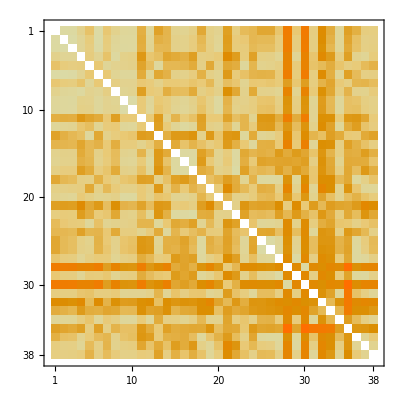

```mathematica
MatrixPlot[
Outer[VA2,vv[[perm[[1]]]],vv[[perm[[1]]]],1]
]
```

```mathematica
Manipulate[
perm=FindClusters[vv->Range[Length[vv]],Max[states],DistanceFunction->VA2,Method->"Optimize"];
permMatrix=IdentityMatrix[Length[vv]][[Flatten@perm]];
mm=Outer[VA2,vv,vv,1];
Grid[{{MatrixPlot[1-permMatrix.mm.Transpose[permMatrix]/Pi*2,FrameTicks->None,FrameTicks->{Automatic,Automatic,None,None}],
Map[({
ListPlot[Table[BestFit[ww,vv[[#[[Round[Length[#]/1]]]]]],{ww,vv[[#]]}],PlotStyle->ToPlotStyle[sList[[#]],{Dashed}],ImageSize->240,FrameTicks->None,PlotRange->{-1,1}*0.7],
ListLogPlot[Table[{iList[[#[[nn]]]],ww[[#[[nn]]]]},{nn,1,Length[#]}],PlotStyle->ToPlotStyle[sList[[#]],{Dashed}],ImageSize->240,FrameTicks->None,PlotRange->{idList,{10,3000}},Joined->True]
})&,perm]}}]
,{{states,4},2,25,1}]
```

```mathematica
Map[({
ListPlot[Table[BestFit[ww,vv[[#[[Round[Length[#]/1]]]]]],{ww,vv[[#]]}],PlotStyle->ToPlotStyle[sList[[#]],{Dashed}],ImageSize->240,FrameTicks->None,PlotRange->{-1,1}*0.7],
Graphics[Riffle[$Colors[[sList[[#]]]],Map[Point,Transpose[{iList[[#]],ww[[#]]}]]],ImageSize->240,FrameTicks->None,PlotRange->{{Min[idList],Max[idList]},{10,3000}},AspectRatio->1]
})&,perm]
```

```mathematica
permMatrix=IdentityMatrix[Length[vv]][[Flatten@FindClusters[vv->Range[Length[vv]],5,DistanceFunction->VA]]];
```

```mathematica
Manipulate[
Table[
listOfEstimationsAll[[2,id,st]],
{st,1,5}]
,{id,1,20,1}]
```

```mathematica
fiberNo=2;
fiberID=2;
```

```mathematica
evList4=Table[
Table[
estim=listOfEstimations4[[fiberNo,nn]];
disc=Op["Discretization"]@listOfTS[[fiberNo,nn]];
Transpose[{-Op["Centers"]@disc,(Op["Projection"]@estim.Op["QMatrix"]@estim)[[All,ev]]}]
,{ev,1,4}
]
,{nn,1,Length[listOfEstimations[[fiberNo]]]}];
```

```mathematica
evList=Table[
Table[
estim=listOfEstimations[[fiberNo,nn]];
disc=Op["Discretization"]@listOfTS[[fiberNo,nn]];
Transpose[{-Op["Centers"]@disc,(Op["Projection"]@estim.Op["QMatrix"]@estim)[[All,ev]]}]
,{ev,1,3}
]
,{nn,1,Length[listOfEstimations[[fiberNo]]]}
];
```

#### 4 States Stuff

```mathematica
vec4id={{1,3,4,2},{1,2,3,4},{1,2,3,4}-1,1,1,1};
vec4orient={1,1,1,1,1,1,1,1,1,1,1,1,1,1,-1,-1,-1,1,1,1};
```

```mathematica
fiberNo=2;
evList4=Table[
estim=SpectralFitting[listOfListOfCM[[fiberNo,nn]],States->4];
disc=Op["Discretization"]@listOfTS[[fiberNo,nn]];
Table[
Transpose[{-Op["Centers"]@disc,(Op["Projection"]@estim.Op["QMatrix"]@estim)[[All,ev]]}]
,{ev,1,4}
]
,{nn,15,17}];
```

```mathematica
prange4={15,16,17};
fiberNo=2;
evalList4=Table[
estim=SpectralFitting[listOfListOfCM[[fiberNo,nn]],States->4];
Reverse@Sort@Op["TimeScales"]@estim
,{nn,prange}];
```

```mathematica
pl1=Graphics[{
Table[
{EdgeForm[Directive[Black,Thickness[0.0015]]],Opacity[0.8],$Colors[[ev*3-4]],Worm[evList[[nn,ev]],{1.0,orientVec[[ev-1,nn]]*4.5},{nn*1.0-0.0,0},0]}
,{ev,2,3}
,{nn,prange}
]
},
AspectRatio->0.5,Frame->True,ImageSize->640, Axes->False,AxesOrigin->{0,1.5},FrameTicks->{None,Automatic,None,None},PlotRange->{{prange[[1]]-0.2,prange[[-1]]+0.2},{1.8,6.8}},PlotRangeClipping->True,PlotRangePadding->Scaled[0.03],
ImagePadding->{{50,1},{2,2}}
];
pl1b=Graphics[{
Table[
{EdgeForm[Directive[Black,Dashing[{0.004,0.004}],Thickness[0.0015]]],Opacity[0.2],$Colors[[ev]],Worm[evList[[nn,ev]],{1.0,2.0},{nn*1.0-0.0,0},-1]}
,{ev,1}
,{nn,prange}
],
Table[
{EdgeForm[Directive[Black,Thickness[0.0015]]],Opacity[0.8],$Colors[[ev*3-1]],Worm[evList[[nn,If[ev==1,mixVec[[nn]],5-mixVec[[nn]]]]],{1.0,orientVec[[ev,nn]]*4.5},{nn*1.0-0.0,0},0]}
,{ev,1,2}
,{nn,prange}
],
Table[
{EdgeForm[Directive[Black,Thickness[0.0015]]],Opacity[0.8],$Colors[[4]],Worm[evList4[[nn,vec4id[[nn,4]]]],{1.0,vec4orient[[nn]]*4.5},{nn*1.0,0},0]}
,{nn,1,3}
]
},
AspectRatio->0.4,Frame->True,ImageSize->480, Axes->False,AxesOrigin->{0,1.5},FrameTicks->{{#,#}&/@prange,Automatic,{#,#}&/@prange,Automatic},PlotRange->{{prange[[1]]-0.2,prange[[-1]]+0.2},{3.0,7.0}},PlotRangeClipping->True,PlotRangePadding->Scaled[0.03],
ImagePadding->{{50,1},{0,2}},
BaseStyle->{FontFamily->"Palatino",FontSize->16}
];
pl2=ListLogPlot[Join[Table[
Transpose[
{
prange,
Transpose[Table[(Op["TimeScales"]@listOfEstimations[[fiberID,estID]])[[{mixVec[[estID]]-1,4-mixVec[[estID]]}]],{estID,prange}]][[nn]]
}
],
{nn,{1,2}}],Table[
Transpose[
{
prange,
Transpose[Table[(Op["TimeScales"]@listOfEstimations4[[fiberID,estID]])[[{mixVec[[estID]]-1,4-mixVec[[estID]]}]],{estID,prange}]][[nn]]
}
],
{nn,{1,2}}]
],ImageSize->480,PlotRangePadding->Scaled[0.03],AspectRatio->0.20,PlotRange->{{prange[[1]]-0.2,prange[[-1]]+0.2},{80,3200}},
FrameTicks->{{#,#}&/@prange,Automatic,{#,#}&/@prange,Automatic},PlotStyle->ToPlotStyle[{2,5,4},Directive[Solid,Thickness[0.008],Opacity[0.8]]],
ImagePadding->{{50,1},{20,0}},FrameLabel->{"",""},
BaseStyle->{FontFamily->"Palatino",FontSize->16}];
pl3=ListLogPlot[
Transpose[{prange,
Map[Op["Residual"],listOfEstimations[[fiberID,prange]]]
}],ImageSize->480,ImagePadding->{{50,0},{80,2}},PlotRangePadding->Scaled[0.02],AspectRatio->0.2,PlotRange->{{prange[[1]]-0.2,prange[[-1]]+0.2},{0.000001,0.02}},
FrameTicks->{{#,#}&/@prange,Automatic,None,None},PlotStyle->ToPlotStyle[{1},Directive[Solid,Thickness[0.008],Opacity[0.8]]],FrameLabel->{"Tweezer Position ID",""}];
```

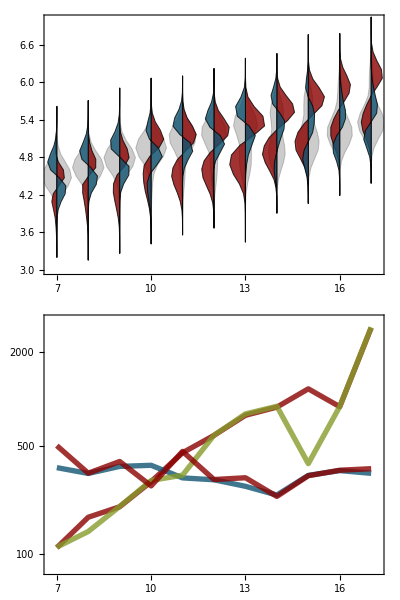

```mathematica
Grid[{
{pl1b},
{pl2}
},
Spacings->{0.001,0.001}
]
```

```mathematica
pl1b=Graphics[{
Table[
{EdgeForm[Directive[Black,Dashing[{0.004,0.004}],Thickness[0.0015]]],Opacity[0.2],$Colors[[ev]],Worm[evList[[nn,ev]],{1.0,2.0},{nn*1.0-0.0,0},-1]}
,{ev,1}
,{nn,prange}
],
Table[
{EdgeForm[Directive[Black,Thickness[0.0015]]],Opacity[0.8],$Colors[[ev*3-1]],Worm[evList[[nn,If[ev==1,mixVec[[nn]],5-mixVec[[nn]]]]],{1.0,orientVec[[ev,nn]]*4.5},{nn*1.0-0.0,0},0]}
,{ev,1,2}
,{nn,prange}
],
Table[
{EdgeForm[Directive[Black,Thickness[0.0015]]],Opacity[0.8],$Colors[[4]],Worm[evList4[[nn,vec4id[[nn,4]]]],{1.0,vec4orient[[nn]]*4.5},{nn*1.0+14,0},0]}
,{nn,1,3}
]
},
AspectRatio->0.4,Frame->True,ImageSize->480, Axes->False,AxesOrigin->{0,1.5},FrameTicks->{{#,#}&/@prange,Automatic,{#,#}&/@prange,Automatic},PlotRange->{{prange[[1]]-0.2,prange[[-1]]+0.2},{3.0,7.0}},PlotRangeClipping->True,PlotRangePadding->Scaled[0.03],
ImagePadding->{{50,1},{0,2}},
BaseStyle->{FontFamily->"Palatino",FontSize->16}
];
pl2=ListLogPlot[Join[Table[
Transpose[
{
prange,
Transpose[Table[(Op["TimeScales"]@listOfEstimations4[[fiberID,estID]])[[{mixVec[[estID]]-1,4-mixVec[[estID]]}]],{estID,prange}]][[nn]]
}
],
{nn,{1,2}}],{
Transpose[
{
prange4,
evalList4[[All,3]]
}
]}
],ImageSize->480,PlotRangePadding->Scaled[0.03],AspectRatio->0.20,PlotRange->{{prange[[1]]-0.2,prange[[-1]]+0.2},{80,3200}},
FrameTicks->{{#,#}&/@prange,Automatic,{#,#}&/@prange,Automatic},PlotStyle->ToPlotStyle[{2,5,4},Directive[Solid,Thickness[0.008],Opacity[0.8]]],
ImagePadding->{{50,1},{20,0}},FrameLabel->{"",""},
BaseStyle->{FontFamily->"Palatino",FontSize->16}];
pl3=ListLogPlot[
Transpose[{prange,
Map[Op["Residual"],listOfEstimations[[fiberID,prange]]]
}],ImageSize->480,ImagePadding->{{50,0},{80,2}},PlotRangePadding->Scaled[0.02],AspectRatio->0.2,PlotRange->{{prange[[1]]-0.2,prange[[-1]]+0.2},{0.000001,0.02}},
FrameTicks->{{#,#}&/@prange,Automatic,None,None},PlotStyle->ToPlotStyle[{1},Directive[Solid,Thickness[0.008],Opacity[0.8]]],FrameLabel->{"Tweezer Position ID",""}];
```

Transpose::nmtx: The first two levels of the one-dimensional list {{15, 16, 17}, {83.74, 140.292, 148.423, 275.339, 153.084, 166.912, 245.006, 235.69, 320.108, 309.693, 307.76}} cannot be transposed.

```mathematica
Grid[{
{pl1b},
{pl2}
},
Spacings->{0.001,0.001}
]
```

#### 3 States Stuff

```mathematica
orientVec={
{1,1,1,1,1,1,-1,-1,1,1,1,1,1,1,1,1,1,1,1,1},
{1,1,1,1,1,1,-1,-1,-1,-1,-1,-1,-1,1,-1,1,-1,1,1,1}
};
mixVec={3,3,3,3,3,3,3,3,3,2,2,2,2,2,2,2,2,3,2,2};
```

```mathematica
listOfEstimations=listOfEstimationsAll[[All,All,2]] (* Estimations for 3 States *)
```

```mathematica
listOfEstimations=
Table[
Table[
SpectralFitting[trace]
,{trace,fiber}
]
,{fiber,listOfListOfCM[[{1,2}]]}
];
```

```mathematica
Table[
Transpose[
{
prange,
Transpose[Table[(Op["TimeScales"]@listOfEstimations[[fiberID,estID]])[[{mixVec[[estID]]-1,4-mixVec[[estID]]}]],{estID,prange}]][[nn]]
}
],
{nn,{1,2}}]
```

{{{7,110.442},{8,173.252},{9,202.28},{10,293.392},{11,449.46},{12,581.291},{13,781.997},{14,882.337},{15,1156.51},{16,887.878},{17,2850.16}},{{7,360.687},{8,331.042},{9,367.388},{10,373.432},{11,309.983},{12,301.389},{13,273.73},{14,240.549},{15,321.68},{16,345.275},{17,331.593}}}

```mathematica
myorange=$Colors[[3]];
$Colors[[3]]=Blend[{RGBColor[0.8958189999999999,0.7313575,0.03721675],Yellow},0.2];
```

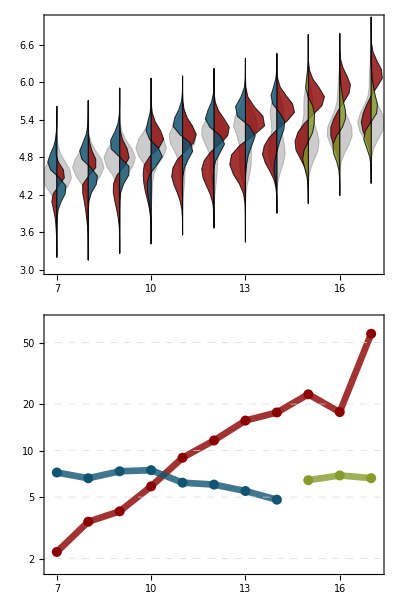

```mathematica
prange=Range[7,17];
pl1=Graphics[{
Table[
{EdgeForm[Directive[Black,Thickness[0.0015]]],Opacity[0.8],$Colors[[ev*3-4]],Worm[evList[[nn,ev]],{1.0,orientVec[[ev-1,nn]]*4.5},{nn*1.0-0.0,0},0]}
,{ev,2,3}
,{nn,prange}
]
},
AspectRatio->0.5,Frame->True,ImageSize->640, Axes->False,AxesOrigin->{0,1.5},FrameTicks->{None,Automatic,None,None},PlotRange->{{prange[[1]]-0.2,prange[[-1]]+0.2},{1.8,6.8}},PlotRangeClipping->True,PlotRangePadding->Scaled[0.03],
ImagePadding->{{50,1},{2,2}}
];
pl1b=Graphics[{
Table[
{EdgeForm[Directive[Black,Dashing[{0.004,0.004}],Thickness[0.0015]]],Opacity[0.2],$Colors[[ev]],Worm[evList[[nn,ev]],{1.0,2.0},{nn*1.0-0.0,0},-1]}
,{ev,1}
,{nn,prange}
],
Table[
{EdgeForm[Directive[Black,Thickness[0.0015]]],Opacity[0.8],If[ev==1||nn<15,$Colors[[3*ev-1]],$Colors[[4]]],Worm[evList[[nn,If[ev==1,mixVec[[nn]],5-mixVec[[nn]]]]],{1.0,orientVec[[ev,nn]]*4.5},{nn*1.0-0.0,0},0]}
,{ev,1,2}
,{nn,prange}
]
},
AspectRatio->0.5,Frame->True,ImageSize->480, Axes->False,AxesOrigin->{0,1.5},FrameTicks->{{#,#}&/@prange,Automatic,{#,#}&/@prange,Automatic},PlotRange->{{prange[[1]]-0.2,prange[[-1]]+0.2},{3.0,7.0}},PlotRangeClipping->True,PlotRangePadding->Scaled[0.03],
ImagePadding->{{50,1},{0,2}},
BaseStyle->{FontFamily->"Palatino",FontSize->16}
];
timeFactor=1/50000*1000;
dataPoints=Join[Table[
Transpose[
{
prange,
timeFactor*Transpose[Table[(Op["TimeScales"]@listOfEstimations[[fiberID,estID]])[[{mixVec[[estID]]-1,4-mixVec[[estID]]}]],{estID,prange}]][[nn]]
}
],
{nn,{1}}],
Table[
Transpose[
{
prange,
timeFactor*Transpose[Table[(Op["TimeScales"]@listOfEstimations[[fiberID,estID]])[[{mixVec[[estID]]-1,4-mixVec[[estID]]}]],{estID,prange}]][[nn]]
}
][[{1,2,3,4,5,6,7,8}]],
{nn,{2}}],
Table[
Transpose[
{
prange,
timeFactor*Transpose[Table[(Op["TimeScales"]@listOfEstimations[[fiberID,estID]])[[{mixVec[[estID]]-1,4-mixVec[[estID]]}]],{estID,prange}]][[nn]]
}
][[{9,10,11}]],
{nn,{2}}]
];
colList={2,5,4};
pl2=ListLogPlot[dataPoints,ImageSize->480,PlotRangePadding->Scaled[0.03],AspectRatio->0.30,PlotRange->{{prange[[1]]-0.2,prange[[-1]]+0.2},{1.7,70}},
FrameTicks->{{#,#}&/@prange,{2,5,10,20,50},{#,#}&/@prange,Automatic},PlotStyle->ToPlotStyle[{2,5,4},Directive[Solid,Thickness[0.01],Opacity[0.8]]],
ImagePadding->{{50,1},{20,0}},FrameLabel->{"",""},
BaseStyle->{FontFamily->"Palatino",FontSize->16},GridLines->{None,{2,5,10,20,50}},GridLinesStyle->Dashed];
pl3=Graphics@Flatten@Table[{PointSize[0.015],$Colors[[colList[[dd]]]],Map[Point[{#[[1]],Log@#[[2]]}]&,dataPoints[[dd]]]},{dd,1,3}];
Graphics[pl3];
Grid[{
{pl1b},
{Show[{pl2,pl3}]}
},
Spacings->{0.1,0.05}
]
```

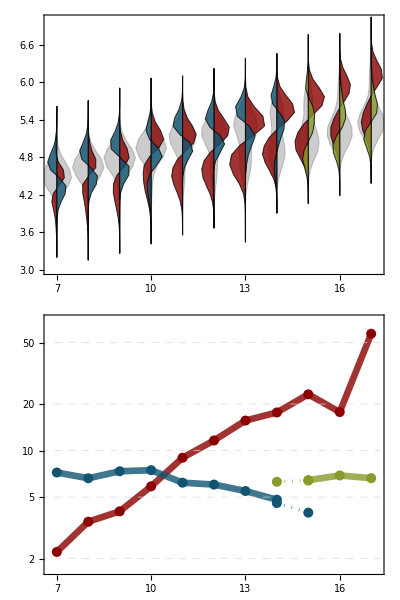

```mathematica
prange=Range[7,17];
pl1=Graphics[{
Table[
{EdgeForm[Directive[Black,Thickness[0.0015]]],Opacity[0.8],$Colors[[ev*3-4]],Worm[evList[[nn,ev]],{1.0,orientVec[[ev-1,nn]]*4.5},{nn*1.0-0.0,0},0]}
,{ev,2,3}
,{nn,prange}
]
},
AspectRatio->0.5,Frame->True,ImageSize->640, Axes->False,AxesOrigin->{0,1.5},FrameTicks->{None,Automatic,None,None},PlotRange->{{prange[[1]]-0.2,prange[[-1]]+0.2},{1.8,6.8}},PlotRangeClipping->True,PlotRangePadding->Scaled[0.03],
ImagePadding->{{50,1},{2,2}}
];
pl1b=Graphics[{
Table[
{EdgeForm[Directive[Black,Dashing[{0.004,0.004}],Thickness[0.0015]]],Opacity[0.2],$Colors[[ev]],Worm[evList[[nn,ev]],{1.0,2.0},{nn*1.0-0.0,0},-1]}
,{ev,1}
,{nn,prange}
],
Table[
{EdgeForm[Directive[Black,Thickness[0.0015]]],Opacity[0.8],If[ev==1||nn<15,$Colors[[3*ev-1]],$Colors[[4]]],Worm[evList[[nn,If[ev==1,mixVec[[nn]],5-mixVec[[nn]]]]],{1.0,orientVec[[ev,nn]]*4.5},{nn*1.0-0.0,0},0]}
,{ev,1,2}
,{nn,prange}
]
},
AspectRatio->0.5,Frame->True,ImageSize->480, Axes->False,AxesOrigin->{0,1.5},FrameTicks->{{#,#}&/@prange,Automatic,{#,#}&/@prange,Automatic},PlotRange->{{prange[[1]]-0.2,prange[[-1]]+0.2},{3.0,7.0}},PlotRangeClipping->True,PlotRangePadding->Scaled[0.03],
ImagePadding->{{50,1},{0,2}},
BaseStyle->{FontFamily->"Palatino",FontSize->16}
];
timeFactor=1/50000*1000;
dataPoints=Join[Table[
Transpose[
{
prange,
timeFactor*Transpose[Table[(Op["TimeScales"]@listOfEstimations[[fiberID,estID]])[[{mixVec[[estID]]-1,4-mixVec[[estID]]}]],{estID,prange}]][[nn]]
}
],
{nn,{1}}],
Table[
Transpose[
{
prange,
timeFactor*Transpose[Table[(Op["TimeScales"]@listOfEstimations[[fiberID,estID]])[[{mixVec[[estID]]-1,4-mixVec[[estID]]}]],{estID,prange}]][[nn]]
}
][[{1,2,3,4,5,6,7,8}]],
{nn,{2}}],
Table[
Transpose[
{
prange,
timeFactor*Transpose[Table[(Op["TimeScales"]@listOfEstimations[[fiberID,estID]])[[{mixVec[[estID]]-1,4-mixVec[[estID]]}]],{estID,prange}]][[nn]]
}
][[{9,10,11}]],
{nn,{2}}],
Table[
Transpose[
{
prange,
timeFactor*Transpose[Table[(Op["TimeScales"]@listOfEstimationsAll[[fiberID,estID,4]])[[If[estID<15,{2,3},{3,2}]]],{estID,prange}]][[nn]]
}
][[{8,9}]],
{nn,{1,2}}],
Table[
Transpose[
{
prange,
timeFactor*Transpose[Table[(Op["TimeScales"]@se)[[{1,2,3,4}]],{estID,prange}]][[nn]]
}
][[{4}]],
{nn,{1,2,3,4}}]
];
colList={2,5,4,5,4,2,1,2,5};
pl2=ListLogPlot[dataPoints[[Range[5]]],ImageSize->480,PlotRangePadding->Scaled[0.03],AspectRatio->0.30,PlotRange->{{prange[[1]]-0.2,prange[[-1]]+0.2},{1.7,70}},
FrameTicks->{{#,#}&/@prange,{2,5,10,20,50},{#,#}&/@prange,Automatic},PlotStyle->ToPlotStyle[{2,5,4,5,4},{
Directive[Solid,Thickness[0.01],Opacity[0.8]],
Directive[Solid,Thickness[0.01],Opacity[0.8]],
Directive[Solid,Thickness[0.01],Opacity[0.8]],
Directive[Dotted,Thickness[0.005],Opacity[0.8]],
Directive[Dotted,Thickness[0.005],Opacity[0.8]]}],
ImagePadding->{{50,1},{20,0}},FrameLabel->{"",""},
BaseStyle->{FontFamily->"Palatino",FontSize->16},GridLines->{None,{2,5,10,20,50}},GridLinesStyle->Dashed];
pl3=Graphics@Flatten@Table[{PointSize[0.015],$Colors[[colList[[dd]]]],Map[Point[{#[[1]],Log@#[[2]]}]&,dataPoints[[dd]]]},{dd,{1,2,3,4,5}}];
Graphics[pl3];
Grid[{
{pl1b},
{Show[{pl2,pl3}]}
},
Spacings->{0.1,0.05}
]
```

```mathematica
ADTicks={{1,"A"},{2,"B"},{3,"C"},{4,"D"}};
Table[
MatrixPlot[
If[no>13&&no<16,tModelEst4[[no,1]],ArrayPad[tModelEst[[no,1]],If[no>15,{1,0},{0,1}],"Fixed"]],ColorFunction->($DefaultColorFunctionWhite[1-(#)]&),ColorFunctionScaling->False,FrameTicks->{ADTicks,ADTicks}]
,{no,Range[7,17]}]
```

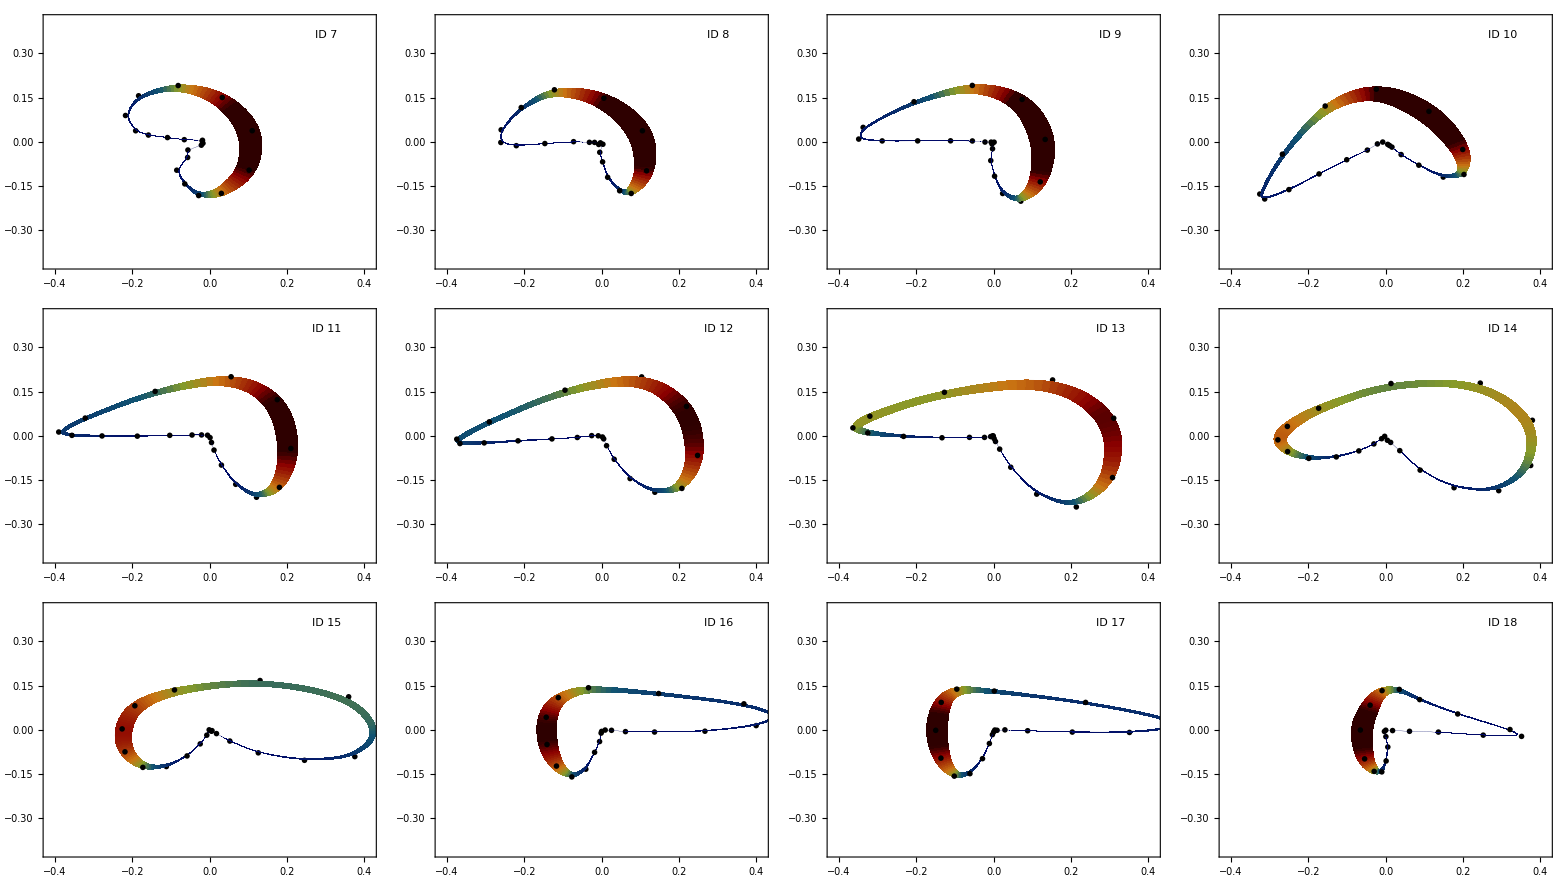

```mathematica
Remove[points]
lagT=40;
tsList=Transpose[Transpose[Table[(Op["TimeScales"]@listOfEstimations[[fiberID,estID]])[[{mixVec[[estID]]-1,4-mixVec[[estID]]}]],{estID,1,20}]][[{1,2}]]]/800;
points[{t1_,t2_},tfunc_]:={f[t1]-tfunc[t1]*df[t1]/2,f[t2]-tfunc[t2]*df[t2]/2,f[t2]+tfunc[t2]*df[t2]/2,f[t1]+tfunc[t1]*df[t1]/2}
q[t_]:=p[t];
thickF[t_]:=(Abs[q[t]])*0.05;
colorF[t_]:=ColorData["DarkRainbow"][2-0.25];
colorF[t_]:=Blend[{$Colors[[2]],Red},0.5];
colorF[t_]:=$DefaultColorFunction[1-q[t]];
scFac=0.5;
Grid[Partition[
Table[
p=Interpolation[Transpose[{Range[0,1,1/(Length@evList[[nn,1,All,2]]-1)],5*Abs@evList[[nn,1,All,2]]}]];
pList=MapIndexed[#*tsList[[nn]]^0*orientVec[[All,nn]]*1/(Abs@evList[[nn,1,#2[[1]],2]])^(scFac)&,Transpose@evList[[nn,{mixVec[[nn]],5-mixVec[[nn]]},All,2]]];
f=BSplineFunction[pList,SplineDegree->2];
df[t_]=Normalize[RotationMatrix[Pi/2].D[f[t],t]];
times=Append[#,First[#]]&@Table[t,{t,0,1,0.005}];
Graphics[{
Text[Style["ID "<>ToString[nn],FontFamily->"Palatino"],Scaled[{0.85,0.92}]],
Flatten@Transpose[{EdgeForm[Directive[#,Thickness[0.0001]]]&/@colorF/@(Drop[times,-1]),colorF/@(Drop[times,-1]), Polygon/@(points[#,thickF]&/@Partition[times,2,1])}],
PointSize[0.020],Black,Map[Point,pList]},PlotRange->{{-1,1},{-1,1}}*0.2/(Max@(Abs@evList[[7,1,All,2]])^(scFac)),
Axes->True,
ImagePadding->1,
ImageSize->200
]
,{nn,7,18}],4],Spacings->{0.01,0.01}]
```

```mathematica
fiberNo=2;
mixinList=Table[
estim=listOfEstimationsAll[[fiberNo,nn,2]];
disc=Op["Discretization"]@listOfTS[[fiberNo,nn]];
mA=Transpose[Op["QMatrix"]@estim];
mAT=Transpose[mA];
mV=Op["Projection"]@estim;
mQ=mV.mAT;
mVT=Transpose[mV];
mPiI=Inverse[DiagonalMatrix[evList[[nn,1,All,2]]]]/Sign[Mean[evList[[nn,1,All,2]]]];
If[!True,
mW=Transpose[Op["Rejection"]@estim];,
mW=mPiI.mQ;
];
mWT=Transpose[mW];
mD=Inverse[mA.mVT.mW].Inverse[mA.Transpose[mA]];
mM=mW.mD.mA.mVT;
mVC=mM.mQ;
{mQ,mW,mVC}
,{nn,1,Length[listOfEstimations[[fiberNo]]]}];
```

```mathematica
fiberNo=2;
mixinList4=Table[
estim=listOfEstimationsAll[[fiberNo,nn,3]];
disc=Op["Discretization"]@listOfTS[[fiberNo,nn]];
mA=Transpose[Op["QMatrix"]@estim];
mAT=Transpose[mA];
mV=Op["Projection"]@estim;
mQ=mV.mAT;
mVT=Transpose[mV];
mPiI=Inverse[DiagonalMatrix[evList[[nn,1,All,2]]]]/Sign[Mean[evList[[nn,1,All,2]]]];
If[!True,
mW=Transpose[Op["Rejection"]@estim];,
mW=mPiI.mQ;
];
mWT=Transpose[mW];
mD=Inverse[mA.mVT.mW].Inverse[mA.Transpose[mA]];
mM=mW.mD.mA.mVT;
mVC=mM.mQ;
{mQ,mW,mVC}
,{nn,1,Length[listOfEstimations[[fiberNo]]]}];
```

```mathematica
Manipulate[
Grid[Partition[Table[
ListPlot[Transpose@mixinList[[nn,pp]],ImageSize->320],
{pp,1,3}],3]],{nn,1,20,1}]
```

```mathematica
cfunc[s_]:=Function[x,If[Abs[x]<s,x/s,Sign[x]]];
estRightEV=Table[
RegularizeLeftEV[Transpose[evecs[[1]]],CutOffFunction->cFunc[0.004]]
,{evecs,mixinList}];
```

```mathematica
cfunc[s_]:=Function[x,If[Abs[x]<s,x/s,Sign[x]]];
estRightEV4=Table[
RegularizeLeftEV[Transpose[evecs[[1]]],CutOffFunction->cFunc[0.004]]
,{evecs,mixinList4}];
```

```mathematica
Grid@Partition[Table[
ListPlot[Join[estRightEV4[[no,{2,3,4}]]],PlotRange->All,ImageSize->240,FrameTicks->None,PlotStyle->ToPlotStyle[{2,If[no<15,5,4],3},{Directive[Thickness[0.01],Solid],Directive[Thickness[0.01],Solid],Directive[Thickness[0.01],Solid],Dashed,Dashed,Dashed}],Filling->{1->{0,Directive[Opacity[0.2],$Colors[[2]]]},2->{0,Directive[Opacity[0.2],$Colors[[If[no<15,5,4]]]]},3->{0,Directive[Opacity[0.2],$Colors[[If[no<15,3,3]]]]}},Axes->{True,False},AxesStyle->Thick],
{no,7,18}
],4]
```

```mathematica
Grid@Partition[Table[
ListPlot[Join[estRightEV4[[no,{2,3,4}]],(-Transpose@mixinList4[[no,2]])[[{2,3,4}]]],PlotRange->All,ImageSize->240,FrameTicks->None,PlotStyle->ToPlotStyle[{2,If[no<15,5,4],3,2,If[no<15,5,4],3},{Directive[Thickness[0.01],Solid],Directive[Thickness[0.01],Solid],Dashed,Dashed}],Filling->{1->{0,Directive[Opacity[0.2],$Colors[[2]]]},2->{0,Directive[Opacity[0.2],$Colors[[If[no<15,5,4]]]]},3->{0,Directive[Opacity[0.2],$Colors[[If[no<15,3,3]]]]}},Axes->{True,False},AxesStyle->Thick],
{no,7,18}
],4]
```

```mathematica
Grid@Partition[Table[
ListPlot[Join[estRightEV[[no,{2,3}]],(-Transpose@mixinList[[no,2]])[[{2,3}]]],PlotRange->All,ImageSize->240,FrameTicks->None,PlotStyle->ToPlotStyle[{2,If[no<15,5,4],2,If[no<15,5,4]},{Directive[Thickness[0.01],Solid],Directive[Thickness[0.01],Solid],Dashed,Dashed}],Filling->{1->{0,Directive[Opacity[0.2],$Colors[[2]]]},2->{0,Directive[Opacity[0.2],$Colors[[If[no<15,5,4]]]]}},Axes->{True,False},AxesStyle->Thick],
{no,7,18}
],4]
```

𝔼[20,5]→{293.542, 73.5593, 304.005, 520.207}

{293.542,73.5593,304.005,520.207}

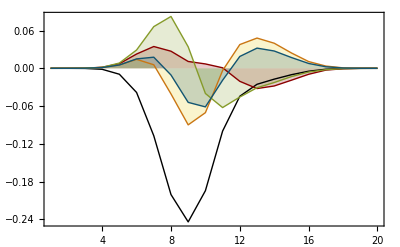

{{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{-1.11429,-1.10055,-1.09101,-0.987316,-0.785249,-0.593208,-0.323585,-0.135707,-0.0446644,-0.0359449,-0.0086892,0.465509,1.26825,1.6307,1.86353,2.06482,1.98079,2.01777,1.96341,1.94441},{-0.930742,-0.914863,-0.902944,-0.83934,-0.591412,-0.372172,-0.0530896,0.202793,0.368144,0.36236,0.035321,-0.85114,-1.89769,-2.32174,-2.41047,-2.33753,-2.43567,-2.41886,-2.43948,-2.44654},{-1.01174,-1.00649,-1.00397,-0.984371,-0.899962,-0.759039,-0.618622,-0.410992,-0.140197,0.205534,0.625214,1.02818,1.21587,1.31249,1.29825,1.28693,1.40202,1.38817,1.42646,1.4391},{-0.797999,-0.785196,-0.779921,-0.732287,-0.569123,-0.390586,-0.165233,0.0528874,0.221741,0.315024,0.189527,-0.425787,-1.2675,-1.60307,-1.6969,-1.68657,-1.69236,-1.69655,-1.68486,-1.6846}}

```mathematica
se=listOfEstimationsAll[[fiberID,10,4]]
Op["TimeScales"]@se
ListPlot[Transpose@(Op["Projection"]@se.Op["QMatrix"]@se),Filling->Table[no->{0,Directive[Opacity[0.2],$Colors[[no]]]},{no,2,Op["States"]@se}],PlotRange->All]
pcca5StID10=EnhancedPCCA[reg5StID10,States->5]
reg5StID10=RegularizeLeftEV[Transpose@(Op["Projection"]@se.Op["QMatrix"]@se)]
```

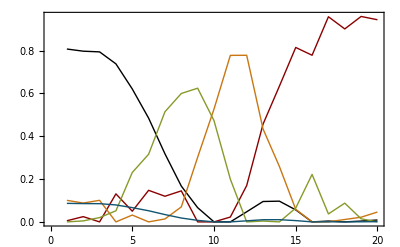

```mathematica
ListPlot[Op["Memberships"]@pcca5StID10]
```

```mathematica
Grid[Partition[Table[
eq=Abs@mixinList[[no,1,All,1]];
ListPlot[Map[#*eq&,Join[estRightEV[[no,{2,3,4}]],(-Transpose@mixinList[[no,2]])[[{2,3}]]]],PlotRange->All,ImageSize->240,FrameTicks->None,PlotStyle->ToPlotStyle[{2,If[no<15,5,4],2,If[no<15,5,4]},{Directive[Thickness[0.01],Solid],Directive[Thickness[0.01],Solid],Dashed,Dashed}],Filling->{1->{0,Directive[Opacity[0.2],$Colors[[2]]]},2->{0,Directive[Opacity[0.2],$Colors[[If[no<15,5,4]]]]}},Axes->{True,False},AxesStyle->Thick],
{no,7,18}
],4],Spacings->{0.01,0.2}]
```

```mathematica
tModelEst=Table[
evals=DiagonalMatrix@Join[{1},Op["Eigenvalues"]@listOfEstimationsAll[[2,no,2]]];
levecs=mixinList[[no,1]];
pi=-levecs[[All,1]];
cMM=levecs.evals.Transpose@levecs;
stDef=pccaAllEstimate[[no,5]];
pMat=stDef.cMM.Transpose[stDef];
mass =stDef.DiagonalMatrix[pi].Transpose[stDef];
pMatSm=Inverse[mass].pMat;
order=Sort[Transpose[{Range[3],Map[Total[#*Range[20]/Total[#]]&,pccaAllEstimate[[no,4]]]}],#1[[2]]<#2[[2]]&][[All,1]];
oMat=IdentityMatrix[3][[order]];
{oMat.pMatSm.Transpose[oMat],oMat.Equilibrium[TransitionMatrix@pMatSm],levecs,oMat.stDef.DiagonalMatrix[pi]}
,{no,1,20}
];
```

Inverse::luc: Result for Inverse of badly conditioned matrix {{0.326844, 0.107423, 0.107447}, {0.107423, 0.0608317, 0.0608451}, {0.107447, 0.0608451, 0.0608584}} may contain significant numerical errors.

```mathematica
tModelEst4=Table[
evals=DiagonalMatrix@Join[{1},Op["Eigenvalues"]@listOfEstimationsAll[[2,no,3]]];
levecs=mixinList4[[no,1]];
pi=-levecs[[All,1]];
cMM=levecs.evals.Transpose@levecs;
stDef=pccaAllEstimate4[[no,5]];
pMat=stDef.cMM.Transpose[stDef];
mass =stDef.DiagonalMatrix[pi].Transpose[stDef];
pMatSm=Inverse[mass].pMat;
order=Sort[Transpose[{Range[4],Map[Total[#*Range[20]/Total[#]]&,pccaAllEstimate4[[no,4]]]}],#1[[2]]<#2[[2]]&][[All,1]];
oMat=IdentityMatrix[4][[order]];
{oMat.pMatSm.Transpose[oMat],oMat.Equilibrium[TransitionMatrix@pMatSm],levecs,oMat.stDef.DiagonalMatrix[pi],mass,stDef,evals,oMat}
,{no,1,20}
];
```

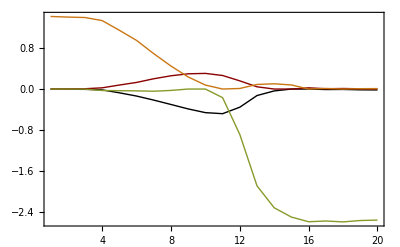
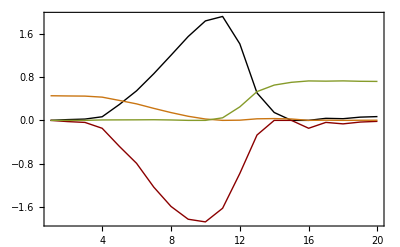
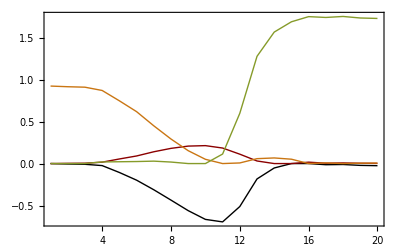

{∞,375.134,298.355,275.339}

```mathematica
{dum1,dum2,levecs,dum4,mass,stDef,evals,oMat}=tModelEst4[[10]];
Table[ListPlot[DiagonalMatrix[Transpose[Inverse[mass].stDef.levecs][[st]]].stDef,PlotRange->All],{st,2,4}]
ToImpliedTimescales[Diagonal@evals,1]
```

```mathematica
Map[Total,tModelEst4[[10,1]]]
```

{1.00062,0.989869,1.00291,1.00694}

(0.481689 | 0.483655 | 0.000742551 | 0.0362324
0.247506 | 0.548046 | 0.192595 | 0.0211466
0.0129274 | 0.0918157 | 0.641049 | 0.248108
0.00538721 | 0.0289238 | 0.593151 | 0.370754)

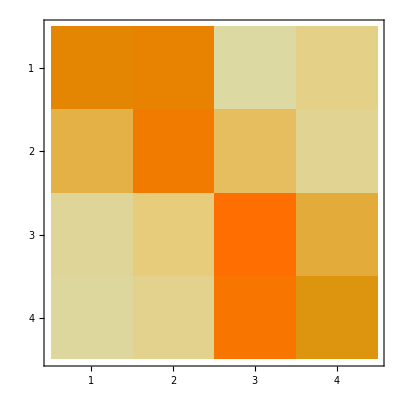

```mathematica
MatrixForm[tModelEst4[[14,1]]]
MatrixPlot[%]
```

```mathematica
evals
```

{{1.,0.,0.,0.},{0.,0.99739,0.,0.},{0.,0.,0.996881,0.},{0.,0.,0.,0.999161}}

```mathematica
levecs.
```

```mathematica
tModelEst4
```

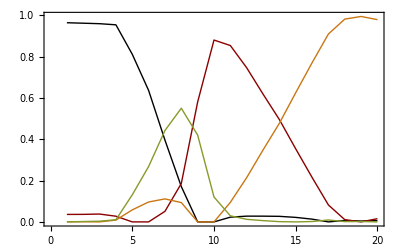

```mathematica
ListPlot[pccaAllEstimate4[[17,5]]]
```

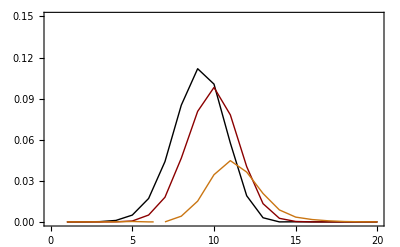
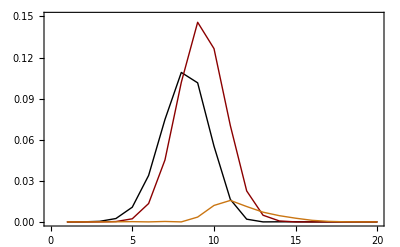
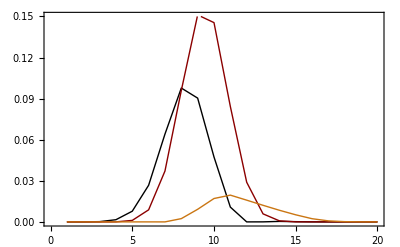
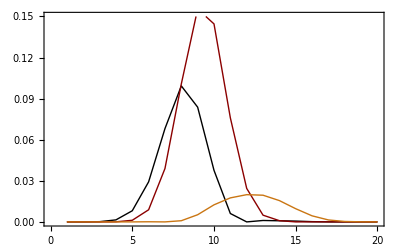
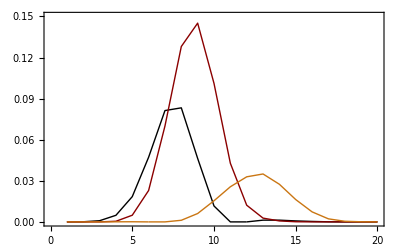
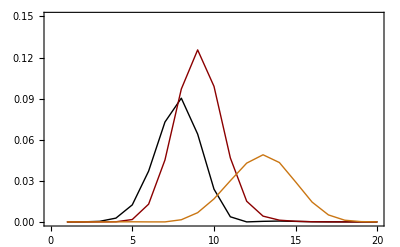
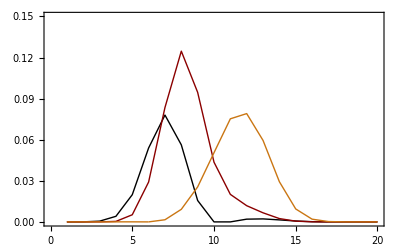
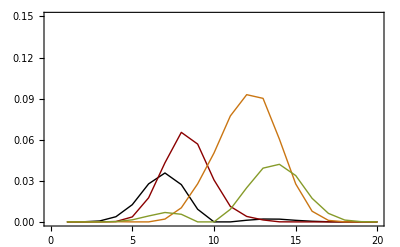

```mathematica
Table[
ListPlot[If[no>13&&no<16,tModelEst4[[no,4]],tModelEst[[no,4]]],PlotRange->{0,0.15}],
{no,prange}]
```

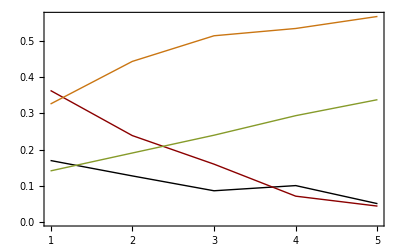

```mathematica
ListPlot[Transpose@tModelEst4[[Range[7,11],2]]]
```

```mathematica
mixL2={
```

```mathematica
Table[
Table[
{nn,tModelEst[[nn,2,st]]}
,{nn,prange}]
,{st,1,3}
]
```

{{{7,0.444445},{8,0.406719},{9,0.347751},{10,0.336318},{11,0.299698},{12,0.311223},{13,0.236554},{14,0.325776},{15,0.215006},{16,0.0792617},{17,0.0690915}},{{7,0.383762},{8,0.53436},{9,0.559749},{10,0.555951},{11,0.534069},{12,0.451637},{13,0.42498},{14,0.0939103},{15,0.0725778},{16,0.472774},{17,0.49098}},{{7,0.171793},{8,0.0589207},{9,0.0925},{10,0.107731},{11,0.166233},{12,0.23714},{13,0.338466},{14,0.580314},{15,0.712416},{16,0.447964},{17,0.439929}}}

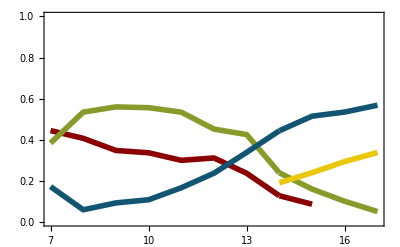

```mathematica
Show[
{
ListPlot[Join[
Table[
Table[
{no,If[no>13&&no<16,tModelEst4[[no,2,st]],tModelEst[[no,2,st]]]}
,{no,Range[7,14]}]
,{st,1,3}
],
Table[
Table[
{no,If[no>15,tModelEst4[[no,2,{2,1,3,4}[[st]]]],tModelEst4[[no,2,st]]]}
,{no,Range[14,If[st==1,15,17]]}]
,{st,1,4}
]
],PlotRange->{0,1},PlotStyle->ToPlotStyle[{2,4,5,2,4,5,3},Directive[Thickness[0.01]]],FrameTicks->{Range[7,17],Automatic,None,Automatic}]
}]
```

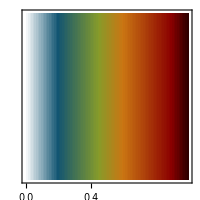

```mathematica
LegendPlot[ColorFunction->($DefaultColorFunctionWhite[1-#]&),RangeText->{"0.0","1.0"},Ticks->Range[0.2,0.8,0.2]]
```

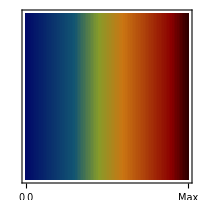

```mathematica
LegendPlot[ColorFunction->($DefaultColorFunction[1-#]&),RangeText->{"0.0","Max"},Ticks->{}]
```

```mathematica
ADTicks={{1,"A"},{2,"B"},{3,"C"},{4,"D"}};
Table[
MatrixPlot[
If[no>13&&no<16,tModelEst4[[no,1]],ArrayPad[tModelEst[[no,1]],If[no>15,{1,0},{0,1}],"Fixed"]],ColorFunction->($DefaultColorFunctionWhite[1-(#)]&),ColorFunctionScaling->False,FrameTicks->{ADTicks,ADTicks}]
,{no,Range[7,17]}]
```

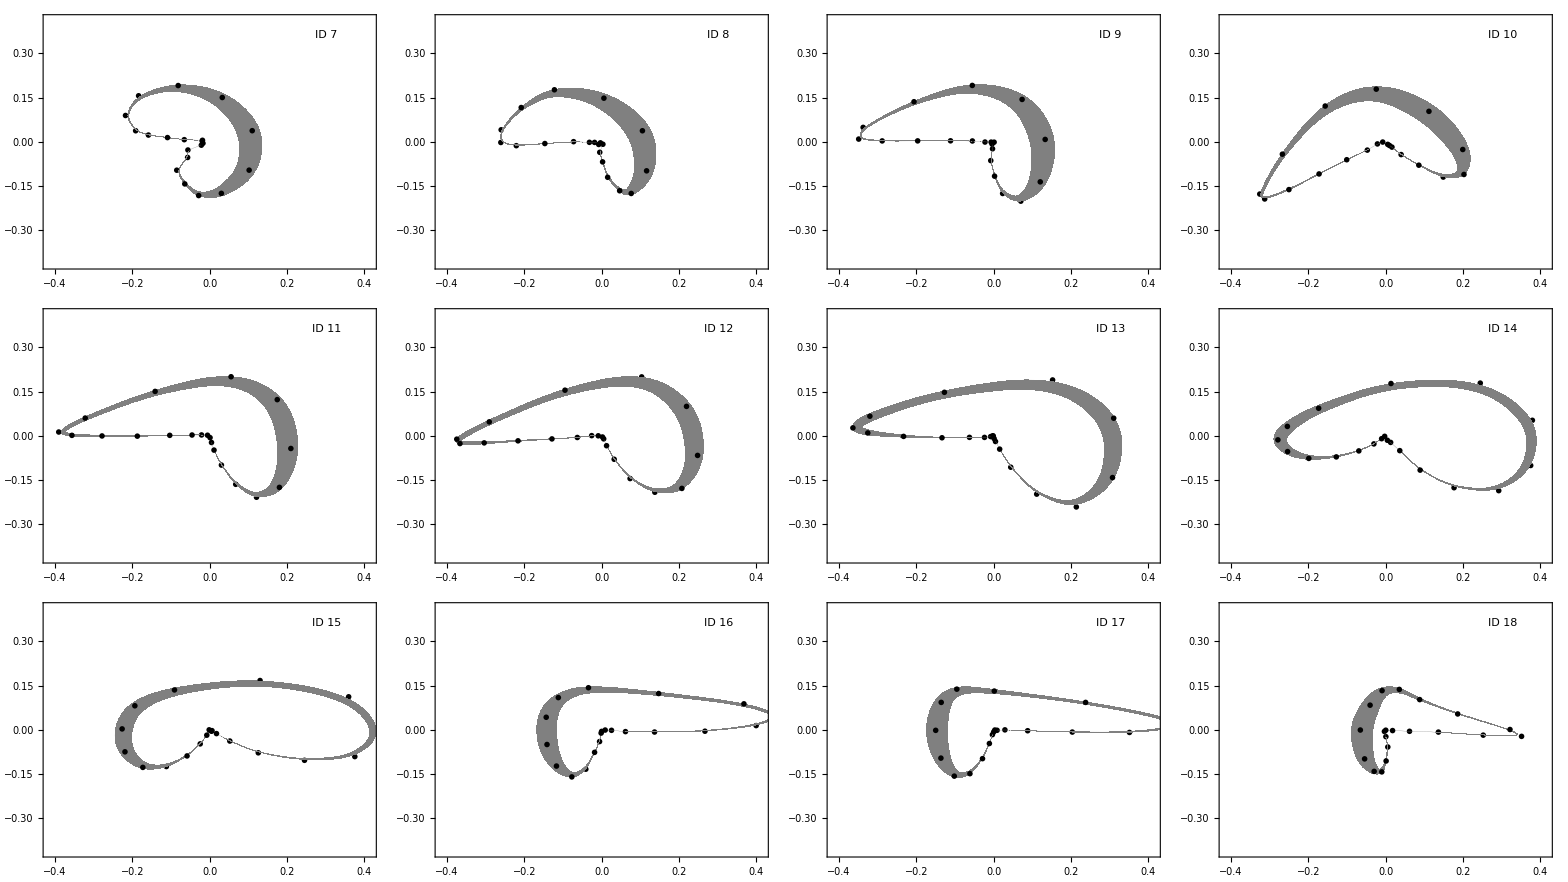

```mathematica
Remove[points]
lagT=40;
tsList=Transpose[Transpose[Table[(Op["TimeScales"]@listOfEstimations[[fiberID,estID]])[[{mixVec[[estID]]-1,4-mixVec[[estID]]}]],{estID,1,20}]][[{1,2}]]]/800;
points[{t1_,t2_},tfunc_]:={f[t1]-tfunc[t1]*df[t1]/2,f[t2]-tfunc[t2]*df[t2]/2,f[t2]+tfunc[t2]*df[t2]/2,f[t1]+tfunc[t1]*df[t1]/2}
q[t_]:=p[t];
thickF[t_]:=(Abs[q[t]])*0.05;
colorF[t_]:=ColorData["DarkRainbow"][2-0.25];
colorF[t_]:=Blend[{$Colors[[2]],Red},0.5];
colorF[t_]:=$DefaultColorFunction[1-q[t]];
colorF[t_]:=Gray;
scFac=0.5;
Grid[Partition[
Table[
p=Interpolation[Transpose[{Range[0,1,1/(Length@evList[[nn,1,All,2]]-1)],5*Abs@evList[[nn,1,All,2]]}]];
pList=MapIndexed[#*tsList[[nn]]^0*orientVec[[All,nn]]*1/(Abs@evList[[nn,1,#2[[1]],2]])^(scFac)&,Transpose@evList[[nn,{mixVec[[nn]],5-mixVec[[nn]]},All,2]]];
f=BSplineFunction[pList,SplineDegree->2];
df[t_]=Normalize[RotationMatrix[Pi/2].D[f[t],t]];
times=Append[#,First[#]]&@Table[t,{t,0,1,0.005}];
Graphics[{Inset[
MatrixPlot[
If[nn>13&&nn<16,tModelEst4[[nn,1]],ArrayPad[tModelEst[[nn,1]],If[nn>15,{1,0},{0,1}],"Fixed"]],
ColorFunction->($DefaultColorFunctionWhite[1-(#)]&),
ColorFunctionScaling->False,
FrameTicks->None,
FrameTicks->{ADTicks,ADTicks}
],
Scaled[{0.02,0.98}],{Left,Top},{0.2,0.2}
],
Text[Style["ID "<>ToString[nn],FontFamily->"Palatino"],Scaled[{0.85,0.92}]],
Flatten@Transpose[{EdgeForm[Directive[#,Thickness[0.0001]]]&/@colorF/@(Drop[times,-1]),colorF/@(Drop[times,-1]), Polygon/@(points[#,thickF]&/@Partition[times,2,1])}],
PointSize[0.020],Black,Map[Point,pList]},PlotRange->{{-1,1},{-1,1}}*0.2/(Max@(Abs@evList[[7,1,All,2]])^(scFac)),
Axes->True,
ImagePadding->1,
ImageSize->200
]
,{nn,7,18}],4],Spacings->{0.01,0.01}]
```

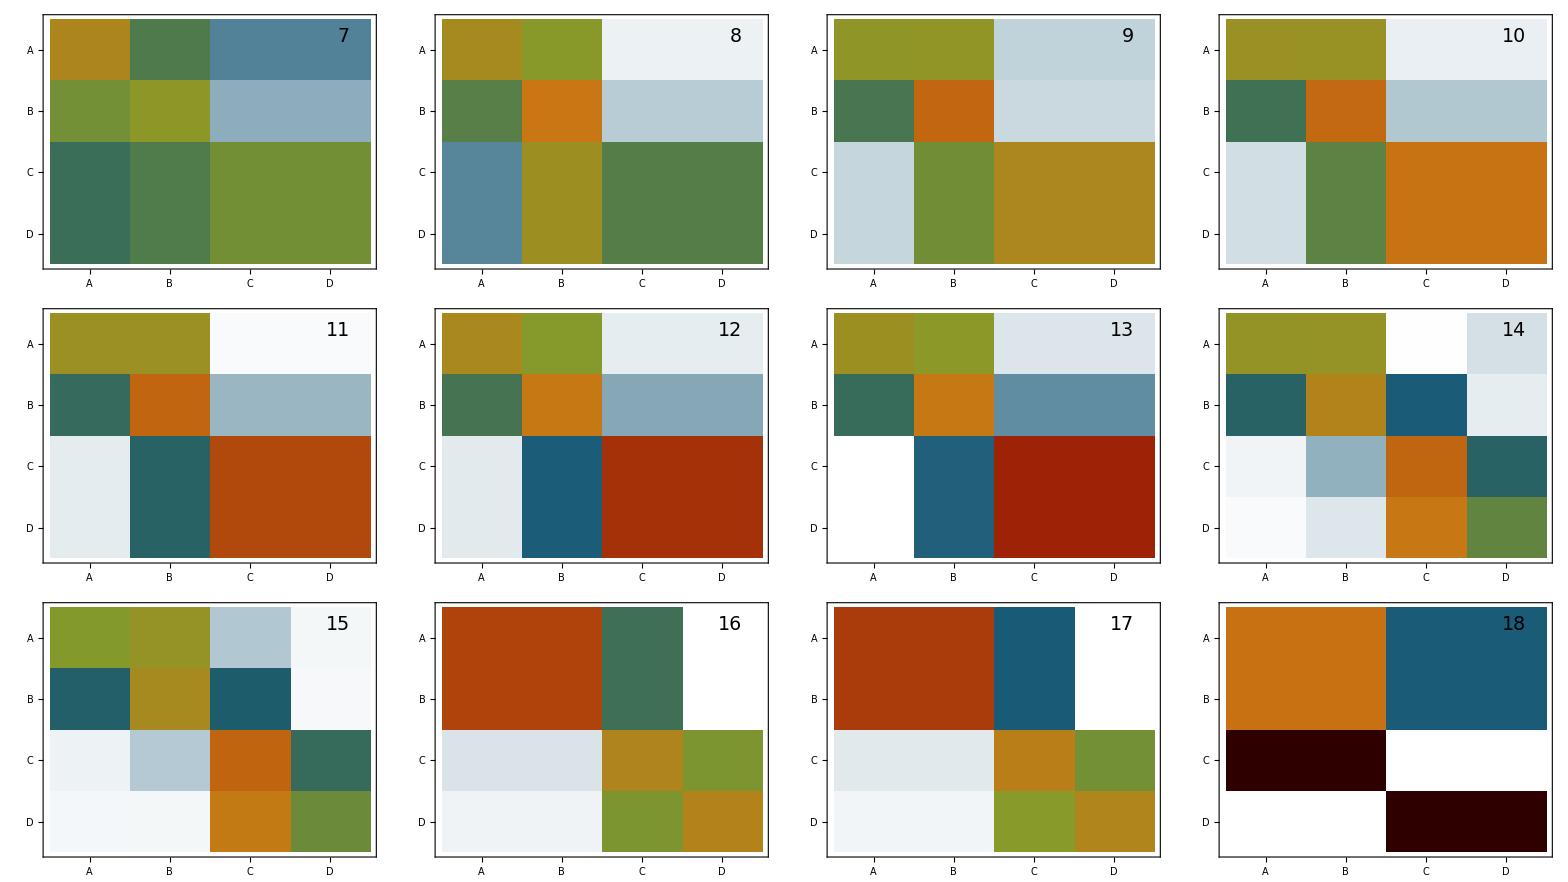

```mathematica
ADTicks={{1,"A"},{2,"B"},{3,"C"},{4,"D"}};
Grid[Partition[Table[
MatrixPlot[
If[no>13&&no<16,tModelEst4[[no,1]],ArrayPad[tModelEst[[no,1]],If[no>15,{1,0},{0,1}],"Fixed"]],ColorFunction->($DefaultColorFunctionWhite[1-(#)]&),ColorFunctionScaling->False,FrameTicks->{ADTicks,ADTicks},ImagePadding->{{1,1},{1,1}},Epilog->{Text[Style[ToString[no],FontSize->19],Scaled[{0.92,0.95}],{1,1}]}]
,{no,Range[7,18]}]
,4]
,Spacings->{0.001,0.001}
]
```

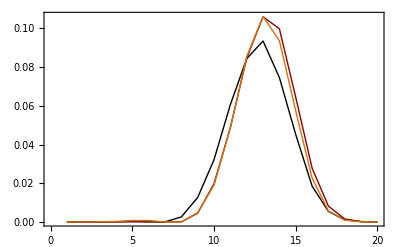

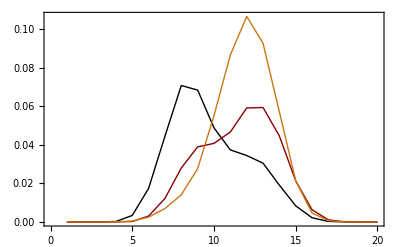

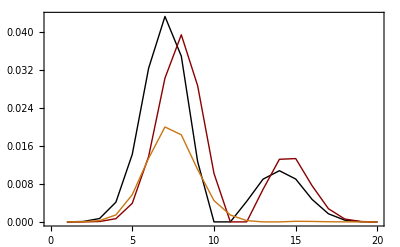

```mathematica
ListPlot[tModelEst[[Range[8,10],4,3]]]
ListPlot[tModelEst[[Range[8,10],4,2]]]
ListPlot[tModelEst[[Range[8,10],4,1]]]
```

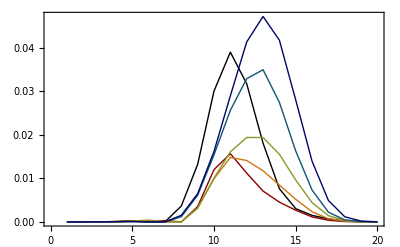

```mathematica
ListPlot[tModelEst[[Range[1,6],4,3]]]
```

```mathematica
Table[
evals=DiagonalMatrix@Join[{1},Op["Eigenvalues"]@listOfEstimationsAll[[2,no,2]]];
levecs=mixinList[[no,1]];
pi=-levecs[[All,1]];
cMM=levecs.evals.Transpose@levecs;
stDef=pccaAllEstimate[[no,5]];
,{no,7,17}
]
```

```mathematica
pMat
pMatSm
```

{{0.272599,0.0732265,0.150395},{0.0732265,0.135098,0.0224585},{0.150395,0.0224585,0.0988179}}

{{0.636146,0.091986,0.276864},{0.201204,0.774446,0.0160456},{0.49401,0.0204422,0.48114}}

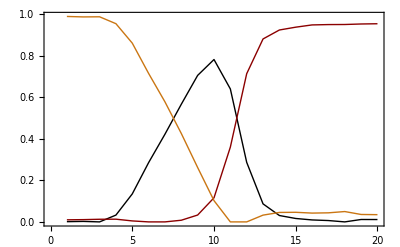

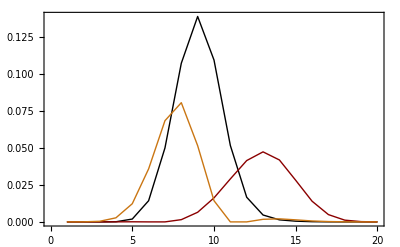

```mathematica
ListPlot[stDef]
ListPlot[stDef.DiagonalMatrix[pi]]
```

```mathematica
Map[Total,stDef.DiagonalMatrix[pi]]
```

{0.495729,0.231946,0.271647}

```mathematica
Equilibrium[TransitionMatrix@pMatSm]
```

{0.498203,0.228564,0.273233}

```mathematica
Map[Total,pMatSm]
```

{1.005,0.991696,0.995592}

```mathematica
pi=-levecs[[All,1]]
```

{4.48896×10^-6,0.000042545,0.000406732,0.0028786,0.0142256,0.0500246,0.118145,0.188905,0.196437,0.139648,0.080518,0.0579881,0.0536313,0.0452214,0.0299041,0.0147082,0.00517839,0.00124057,0.00019669,0.0000188678}

```mathematica
estRightEV[[12]].cMM
```

{{4.46914×10^-6,0.00004238,0.000404751,0.00286637,0.0141809,0.0499384,0.118093,0.189072,0.196848,0.139996,0.0805347,0.0577277,0.0532546,0.0448723,0.0296677,0.0145903,0.00513672,0.00123051,0.000195213,0.0000187107},{-3.37189×10^-6,-0.000027246,-0.00021746,-0.00147044,-0.00721212,-0.0244012,-0.0545821,-0.0792582,-0.0679227,-0.0242298,0.0212686,0.0504498,0.0617197,0.0552753,0.0372447,0.0186028,0.00656287,0.00157411,0.00026041,0.0000276586},{-1.64379×10^-6,-0.0000132715,-0.000130917,-0.000833192,-0.00345733,-0.00897917,-0.0141067,-0.0100026,0.00351357,0.0117483,0.00951273,0.00593424,0.00431914,0.00329798,0.0021538,0.00107698,0.000375963,0.000087303,0.0000218299,2.2434×10^-6}}

```mathematica
Inverse[mass]
```

{{6.44326,-1.71178,-6.61546},{-1.71178,6.44368,1.30314},{-6.61546,1.30314,14.6411}}

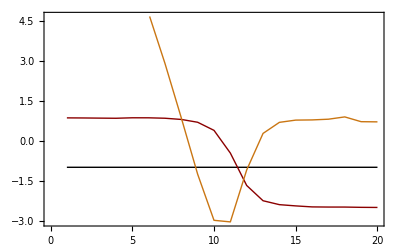

```mathematica
ListPlot[corRight]
```

```mathematica
corRight=Table[estRightEV[[12,nn]]/(estRightEV[[12,nn]].levecs[[All,nn]]),{nn,1,3}]
```

{{-1.00068,-1.00068,-1.00068,-1.00068,-1.00068,-1.00068,-1.00068,-1.00068,-1.00068,-1.00068,-1.00068,-1.00068,-1.00068,-1.00068,-1.00068,-1.00068,-1.00068,-1.00068,-1.00068,-1.00068},{0.854095,0.850699,0.844676,0.839447,0.857244,0.856415,0.840418,0.795013,0.68968,0.385378,-0.466821,-1.6836,-2.2561,-2.4031,-2.44977,-2.48756,-2.49317,-2.49364,-2.50387,-2.50798},{8.60068,8.57579,8.59362,8.14028,6.80895,4.7785,2.89856,0.852753,-1.26024,-2.99089,-3.05028,-1.10069,0.270509,0.685988,0.770237,0.777367,0.804283,0.89048,0.711122,0.704355}}

```mathematica
corRight.levecs
```

{{1.,-0.00381695,0.00399865},{-0.00533002,1.,0.0736593},{0.0224675,0.295074,1.}}

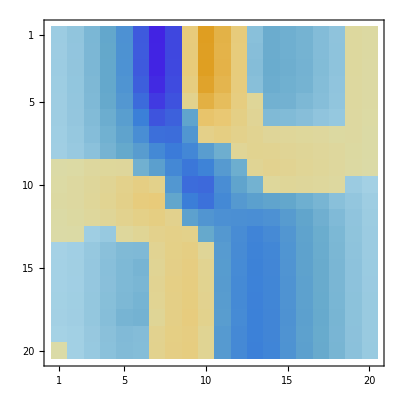

```mathematica
Transpose[-corRight].Transpose[levecs];
MatrixPlot@%
```

```mathematica
mass=Transpose[levecs].levecs
```

{{0.126351,-0.0384846,0.00769864},{-0.0384846,0.051397,0.00279744},{0.00769864,0.00279744,0.0163572}}

```mathematica
cMM
```

```mathematica
cM=Q.L.QT
```

```mathematica
cMC=P.Q.L.QT.PT
```

```mathematica
tM=R.cM.QT
```

```mathematica
cM=P.CMC.PT
```

```mathematica
tMC=Q.QT
```

```mathematica
pro.cM.T[pro]
```

```mathematica
Total@Flatten@pMat
```

0.998675

```mathematica
mixinList[[12,1]]
```

{{-4.48896×10^-6,4.09279×10^-6,8.16892×10^-6},{-0.000042545,0.0000330307,0.0000661004},{-0.000406732,0.000252589,0.000673501},{-0.0028786,0.00172905,0.00425686},{-0.0142256,0.00874567,0.0172491},{-0.0500246,0.0307248,0.0427161},{-0.118145,0.0712083,0.0611946},{-0.188905,0.107706,0.0287861},{-0.196437,0.0971608,-0.0442378},{-0.139648,0.038596,-0.0746367},{-0.080518,-0.0269566,-0.0438883},{-0.0579881,-0.0700162,-0.0114056},{-0.0536313,-0.0867756,0.00259248},{-0.0452214,-0.0779358,0.00554341},{-0.0299041,-0.0525384,0.00411597},{-0.0147082,-0.0262394,0.00204316},{-0.00517839,-0.0092586,0.00074354},{-0.00124057,-0.00222188,0.00019488},{-0.00019669,-0.000364391,-0.0000106134},{-0.0000188678,-0.00003872,-7.43389×10^-7}}

```mathematica
pMat
```

{{0.270793,0.0752373,0.150121},{0.0752373,0.130885,0.0247035},{0.150121,0.0247035,0.09687}}

```mathematica
mass
```

{{2.20909,0.711666,1.11056},{0.711666,7.68268,0.383843},{1.11056,0.383843,5.69609}}

```mathematica
pMatSm
```

{{0.12173,0.0307659,0.0668812},{-0.0016195,0.0143177,-0.00318881},{0.00273056,-0.00262631,0.00418152}}

```mathematica
Map[#/Total[#]&,pMat]
```

```mathematica
ListPlot[stDef]
```

-Graphics-

{6.67977,{a21→0.0938907,a22→0.0720781,a23→0.219705,a31→0.558733,a32→0.354384,a33→-0.144036}}

{{0.347377,-0.426462,-0.0756692},{0.0938907,0.0720781,0.219705},{0.558733,0.354384,-0.144036}}

{0.0206154,0.0200642,0.0131992}

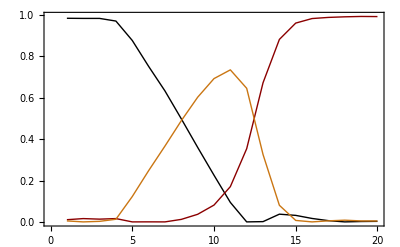

```mathematica
index=9;
alpha={{1.-a21-a31,-(a22+a32),-(a23+a33)},{a21,a22,a23},{a31,a32,a33}};
vTilde=estRightEV[[index]];
posi=Range[20]/20;
means=Map[Total,(alpha.vTilde).DiagonalMatrix@posi]/Map[Total,(alpha.vTilde)]*1.;
variances=Map[Total,(alpha.vTilde).DiagonalMatrix@(posi^2)]/Map[Total,(alpha.vTilde)];
constr=Flatten@Map[Thread,Thread[alpha.vTilde>0]];
minimizer=Chop[Total@Diagonal@Sqrt@Abs@Outer[Dot,(alpha.vTilde),(alpha.vTilde),1]//Simplify];
If[False,constr=Join[constr,{a21>0.01,a31>0.01,a21+a31<0.99}]]
erg=NMaximize[{minimizer,constr},{a21,a22,a23,a31,a32,a33},MaxIterations->2000]
alphaEst=alpha/.erg[[2]]
(variances-means^2)/.erg[[2]]
ListPlot[alphaEst.vTilde]
```

```mathematica
erg2=FindMinimum[{minimizer,constr},{{a21,1/3},{a22,1/3},{a23,0.0},{a31,a32,a33}]
```

```mathematica
index=11;
minimizer=Chop[Total@Flatten[alpha.vTilde*(1-alpha.vTilde)]+Total@Flatten[({{0,0,0},{1,0,0},{1,1,0}}*Outer[Dot,(alpha.vTilde),(alpha.vTilde),1])//Simplify]//Simplify];
alpha={{1.-a21-a31,-(a22+a32),-(a23+a33)},{a21,a22,a23},{a31,a32,a33}};
vTilde=estRightEV[[index]];
posi=Range[20]/20;
means=Map[Total,(alpha.vTilde).DiagonalMatrix@posi]/Map[Total,(alpha.vTilde)]*1.;
variances=Map[Total,(alpha.vTilde).DiagonalMatrix@(posi^2)]/Map[Total,(alpha.vTilde)];
minimizer=Total@(variances-means^2)-Total@Map[Max,alpha.vTilde];
constr=Flatten@Map[Thread,Thread[alpha.vTilde>0]];
If[False,constr=Join[constr,{a21>0.01,a31>0.01,a21+a31<0.99}]]
erg=NMinimize[{minimizer,constr},{a21,a22,a23,a31,a32,a33}]
alphaEst=alpha/.erg[[2]]
(variances-means^2)/.erg[[2]]
```

{-2.66126,{a21→0.172817,a22→0.366158,a23→0.00710447,a31→0.528208,a32→-0.244878,a33→0.398872}}

{{0.298976,-0.121281,-0.405977},{0.172817,0.366158,0.00710447},{0.528208,-0.244878,0.398872}}

{0.0255667,0.0229895,0.017456}

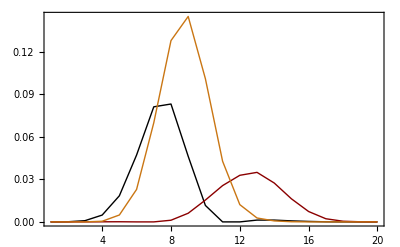

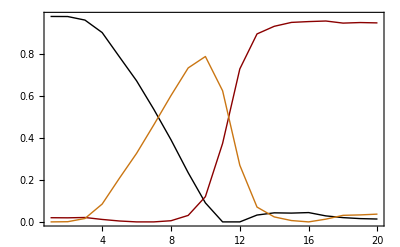

```mathematica
ListPlot[alphaEst.vTilde.DiagonalMatrix[-mixinList[[index,1,All,1]]],PlotRange->All]
ListPlot[alphaEst.vTilde,PlotRange->All]
```

```mathematica
EnhancedPCCA[estRightEV[[12]],States->3]
```

PCCAEstimation[Memberships→{{0.000988029,0.00213603,6.25056×10^-14,0.0297094,0.122107,0.25868,0.382764,0.513446,0.639342,0.708585,0.58019,0.259901,0.0786428,0.0278331,0.0149115,0.00856,0.00587683,4.03774×10^-14,0.0104857,0.0103026},{0.0103568,0.0113033,0.0131387,0.0135462,0.00488915,5.47427×10^-14,5.65745×10^-14,0.00832134,0.0342854,0.120356,0.373505,0.740099,0.913733,0.958477,0.97256,0.983811,0.985546,0.985905,0.988492,0.989697},{0.988655,0.986561,0.986861,0.956744,0.873004,0.74132,0.617236,0.478233,0.326373,0.171059,0.0463046,2.95042×10^-14,0.00762442,0.0136904,0.0125289,0.00762874,0.00857731,0.0140955,0.00102181,2.70811×10^-13}},EigenvectorsRight→{{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{-0.61253,-0.610094,-0.605774,-0.602025,-0.614788,-0.614194,-0.602721,-0.570158,-0.494616,-0.276381,0.334789,1.20742,1.618,1.72343,1.75689,1.784,1.78802,1.78836,1.7957,1.79865},{-1.53691,-1.53247,-1.53565,-1.45464,-1.21674,-0.853902,-0.517963,-0.152384,0.225201,0.534463,0.545075,0.196689,-0.048339,-0.122584,-0.137639,-0.138913,-0.143723,-0.159126,-0.127075,-0.125866}},EstimationResult→{6.65227,{a0201→0.242467,a0202→0.41445,a0203→-0.0141539,a0301→0.310183,a0302→-0.197828,a0303→-0.362607}},States→3,Residual→0.0000391775]

```mathematica
Dynamic[index]
pccaAllEstimate4=
Table[
res=EnhancedPCCA[estRightEV4[[index]],States->4];
{alphaEst,vTilde,-mixinList4[[index,1,All,1]],alphaEst.vTilde.DiagonalMatrix[-mixinList4[[index,1,All,1]]],alphaEst.vTilde},
{index,1,20}
];
```

```mathematica
Export[ToResourceFile["pccaEstimate4.m"],pccaAllEstimate4];
```

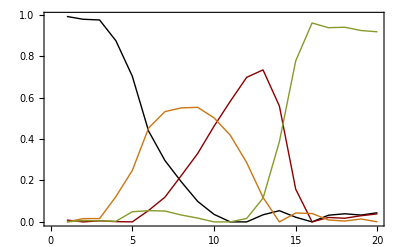

```mathematica
ListPlot[pccaAllEstimate4[[7,5]]]
```

```mathematica
Dynamic[index]
pccaAllEstimate=
Table[
res=EnhancedPCCA[estRightEV[[index]],States->3];
{alphaEst,vTilde,-mixinList[[index,1,All,1]],alphaEst.vTilde.DiagonalMatrix[-mixinList[[index,1,All,1]]],alphaEst.vTilde},
{index,1,20}
];
```

NMaximize::incst: NMaximize was unable to generate any initial points satisfying the inequality constraints {-1.\ a21 - 0.349997\ a22 - 3.80064\ a23 ≤ 0, -1.\ a21 - 0.347878\ a22 - 3.78192\ a23 ≤ 0, -1.\ a21 - 0.357283\ a22 - 3.77914\ a23 ≤ 0, -1.\ a21 - 0.364593\ a22 - 3.77244\ a23 ≤ 0, -1.\ a21 - 0.319602\ a22 - 3.73319\ a23 ≤ 0, -1.\ a21 - 0.339957\ a22 - 3.36593\ a23 ≤ 0, -1.\ a21 - 0.548889\ a22 - 2.27831\ a23 ≤ 0, -1.\ a21 - 0.725949\ a22 - 1.21111\ a23 ≤ 0, « 35 », -1.\ a31 + 0.442541\ a32 + 0.160521\ a33 ≤ 0, -1.\ a31 + 0.13901\ a32 + 0.233068\ a33 ≤ 0, -1. + 1.\ a21 - 1.05967\ a22 + 0.302615\ a23 + 1.\ a31 - 1.05967\ a32 + 0.302615\ a33 ≤ 0, -1. + 1.\ a21 + 0.6823\ a22 + 0.441153\ a23 + 1.\ a31 + 0.6823\ a32 + 0.441153\ a33 ≤ 0, -1. + 1.\ a21 - 1.43014\ a22 + 0.793138\ a23 + 1.\ a31 - 1.43014\ a32 + 0.793138\ a33 ≤ 0, -1. + 1.\ a21 - 1.6695\ a22 + 1.04529\ a23 + 1.\ a31 - 1.6695\ a32 + 1.04529\ a33 ≤ 0, -1. + 1.\ a21 - 1.67261\ a22 + 1.05317\ a23 + 1.\ a31 - 1.67261\ a32 + 1.05317\ a33 ≤ 0, « 10 »}. The initial region specified may not contain any feasible points. Changing the initial region or specifying explicit initial points may provide a better solution.

NMaximize::incst: NMaximize was unable to generate any initial points satisfying the inequality constraints {-1.\ a21 - 0.0782234\ a22 - 0.227513\ a23 ≤ 0, -1.\ a21 + 0.210355\ a22 - 0.223592\ a23 ≤ 0, -1.\ a21 + 0.473095\ a22 - 0.0816129\ a23 ≤ 0, -1.\ a21 - 0.353533\ a22 - 0.0764497\ a23 ≤ 0, -1.\ a21 + 0.730606\ a22 + 0.114798\ a23 ≤ 0, -1.\ a21 - 0.616096\ a22 + 0.26338\ a23 ≤ 0, -1.\ a21 + 0.95765\ a22 + 0.433474\ a23 ≤ 0, -1.\ a21 - 0.810607\ a22 + 0.954628\ a23 ≤ 0, -1.\ a21 + 1.25757\ a22 + 1.12882\ a23 ≤ 0, -1.\ a21 + 1.43532\ a22 + 1.43514\ a23 ≤ 0, « 32 », -1.\ a31 + 0.730606\ a32 + 0.114798\ a33 ≤ 0, -1. + 1.\ a21 - 0.210355\ a22 + 0.223592\ a23 + 1.\ a31 - 0.210355\ a32 + 0.223592\ a33 ≤ 0, -1. + 1.\ a21 + 0.0782234\ a22 + 0.227513\ a23 + 1.\ a31 + 0.0782234\ a32 + 0.227513\ a33 ≤ 0, -1.\ a31 - 0.616096\ a32 + 0.26338\ a33 ≤ 0, -1.\ a31 + 0.95765\ a32 + 0.433474\ a33 ≤ 0, -1.\ a31 - 0.810607\ a32 + 0.954628\ a33 ≤ 0, -1.\ a31 + 1.25757\ a32 + 1.12882\ a33 ≤ 0, -1.\ a31 + 1.43532\ a32 + 1.43514\ a33 ≤ 0, « 10 »}. The initial region specified may not contain any feasible points. Changing the initial region or specifying explicit initial points may provide a better solution.

NMaximize::incst: NMaximize was unable to generate any initial points satisfying the inequality constraints {-1.\ a21 + 0.213593\ a22 - 0.252535\ a23 ≤ 0, -1.\ a21 + 0.503988\ a22 - 0.219825\ a23 ≤ 0, -1.\ a21 + 0.761647\ a22 - 0.213053\ a23 ≤ 0, -1.\ a21 - 0.0750426\ a22 - 0.210091\ a23 ≤ 0, -1.\ a21 + 1.04966\ a22 - 0.132815\ a23 ≤ 0, -1.\ a21 + 1.25908\ a22 - 0.0562563\ a23 ≤ 0, -1.\ a21 - 0.336077\ a22 - 0.0128124\ a23 ≤ 0, -1.\ a21 + 1.41751\ a22 + 0.0403168\ a23 ≤ 0, « 35 », -1.\ a31 + 1.44468\ a32 + 0.0751812\ a33 ≤ 0, -1.\ a31 + 1.46104\ a32 + 0.101644\ a33 ≤ 0, -1. + 1.\ a21 - 1.04966\ a22 + 0.132815\ a23 + 1.\ a31 - 1.04966\ a32 + 0.132815\ a33 ≤ 0, -1. + 1.\ a21 + 0.0750426\ a22 + 0.210091\ a23 + 1.\ a31 + 0.0750426\ a32 + 0.210091\ a33 ≤ 0, -1. + 1.\ a21 - 0.761647\ a22 + 0.213053\ a23 + 1.\ a31 - 0.761647\ a32 + 0.213053\ a33 ≤ 0, -1. + 1.\ a21 - 0.503988\ a22 + 0.219825\ a23 + 1.\ a31 - 0.503988\ a32 + 0.219825\ a33 ≤ 0, -1. + 1.\ a21 - 0.213593\ a22 + 0.252535\ a23 + 1.\ a31 - 0.213593\ a32 + 0.252535\ a33 ≤ 0, « 10 »}. The initial region specified may not contain any feasible points. Changing the initial region or specifying explicit initial points may provide a better solution.

General::stop: Further output of NMaximize :: incst will be suppressed during this calculation.

```mathematica
Export[ToResourceFile["pccaEstimate.m"],pccaAllEstimate]
```

/Users/jan-hendrikprinz/Studium/Projekte/reports/prinz/PrinzEtAl_PMMTheoryLetter/PMMTheoryLett/resources/pccaEstimate.m

```mathematica
Map[Mean[#*Range[20]/Total[#]]&,pccaAllEstimate[[12,4]]]
```

{0.453444,0.646571,0.38688}

{9.86948×10^-9,4.0445×10^-7,2.84251×10^-13,0.000761227,0.0193268,0.172774,0.704405,1.72666,2.51523,2.20194,1.1435,0.402445,0.122011,0.0392115,0.0148841,0.00448262,0.00115124,3.09574×10^-11,0.0000871991,8.65117×10^-6}

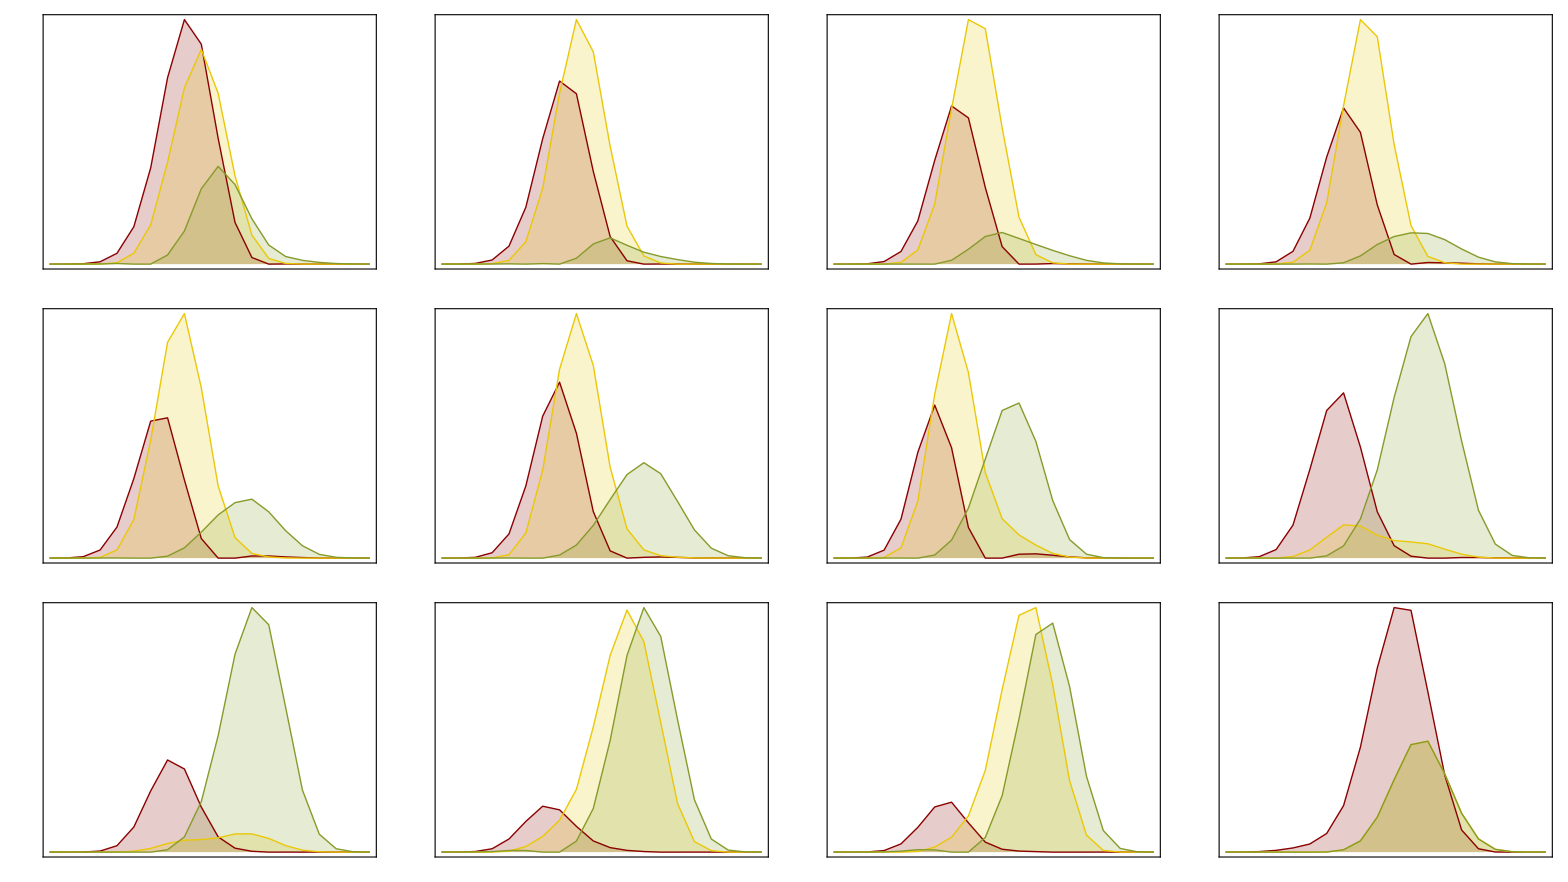

```mathematica
Grid[Partition[Table[
order=Sort[Transpose[{Range[3],Map[Total[#*Range[20]/Total[#]]&,pccaAllEstimate[[no,4]]]}],#1[[2]]<#2[[2]]&][[All,1]];ListPlot[pccaAllEstimate[[no,4,order]],PlotRange->All,ImageSize->240,FrameTicks->None,PlotStyle->ToPlotStyle[{2,3,4},Solid],Filling->{1->{0,Directive[Opacity[0.2],$Colors[[2]]]},2->{0,Directive[Opacity[0.2],$Colors[[3]]]},3->{0,Directive[Opacity[0.2],$Colors[[4]]]}},Axes->{True,False},AxesStyle->Thick],
{no,7,18}
],4],Spacings->{0.01,0.2}]
```

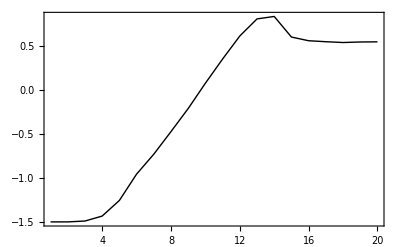

```mathematica
ListPlot[estRightEV[[7,2]],PlotRange->All]
```

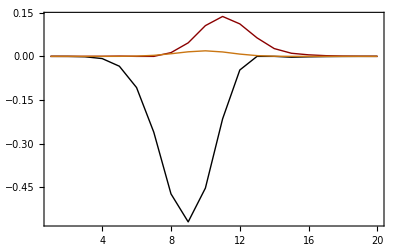
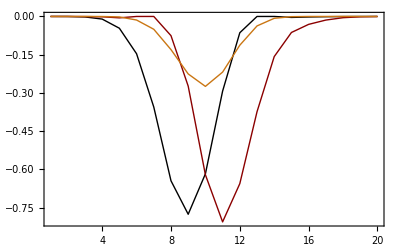
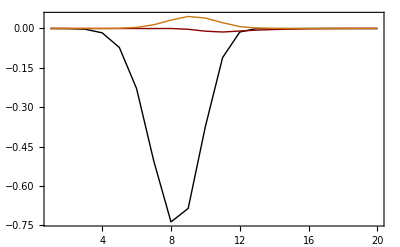
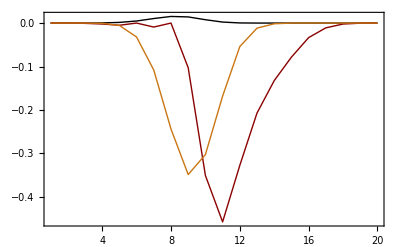
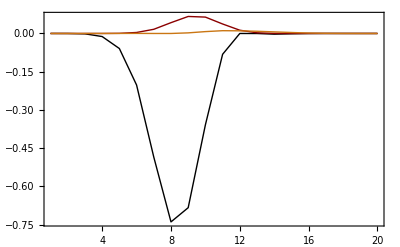
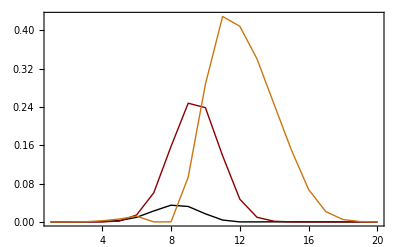
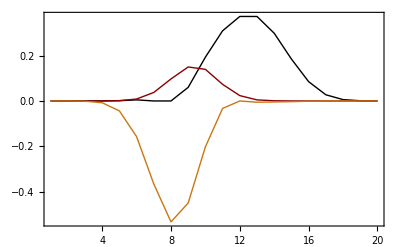
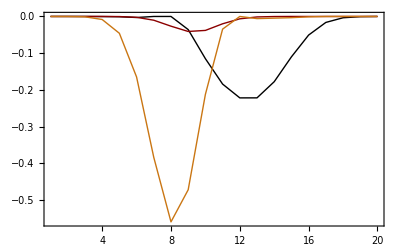

```mathematica
Table[
{
ListPlot[DiagonalMatrix[pccaAllEstimate[[no,5,order]].estRightEV[[no,2]]].pccaAllEstimate[[no,4,order]],PlotRange->All],
ListPlot[DiagonalMatrix[pccaAllEstimate[[no,5,order]].estRightEV[[no,3]]].pccaAllEstimate[[no,4,order]],PlotRange->All]
},
{no,7,17}
]
```

```mathematica
Grid[Partition[Table[
evec=estRightEV[[no,2]];
order=Sort[Transpose[{Range[3],Map[Total[#*Range[20]/Total[#]]&,pccaAllEstimate[[no,4]]]}],#1[[2]]<#2[[2]]&][[All,1]];ListPlot[-pccaAllEstimate[[no,5,order]].Transpose[mixinList[[no,2,1]]],PlotRange->All,ImageSize->240,FrameTicks->None,PlotStyle->ToPlotStyle[{2,3,4},Solid],Filling->{1->{0,Directive[Opacity[0.2],$Colors[[2]]]},2->{0,Directive[Opacity[0.2],$Colors[[3]]]},3->{0,Directive[Opacity[0.2],$Colors[[4]]]}},Axes->{True,False},AxesStyle->Thick],
{no,7,18}
],4],Spacings->{0.01,0.2}]
```

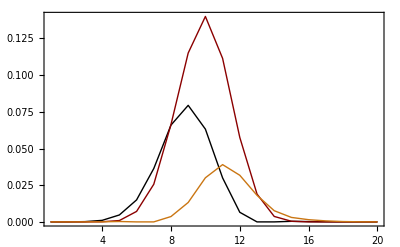

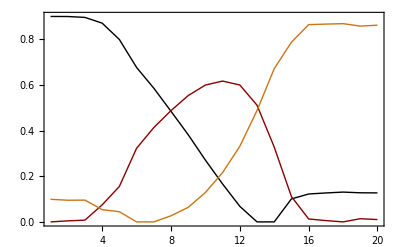

```mathematica
{alphaEst,vTilde,pi,leftEst,rightEst}=pccaAllEstimate[[7]];
ListPlot[leftEst,PlotRange->All]
ListPlot[rightEst,PlotRange->All]
```

```mathematica
index=9;
alpha={{1.-a21-a31,-(a22+a32),-(a23+a33)},{a21,a22,a23},{a31,a32,a33}};
vTilde=estRightEV[[index]];
posi=Range[20];
pi=mixinList[[index,1,All,1]]/Sign[Mean[mixinList[[index,1,All,1]]]];
means=Map[Total,(alpha.vTilde).DiagonalMatrix[posi*pi]]/alpha[[All,1]];
variances=Map[Total,(alpha.vTilde).DiagonalMatrix@(pi*posi^2)]/alpha[[All,1]];
minimizer=Total@((variances-means^2));
constr=Flatten@Map[Thread,Thread[alpha.vTilde>0]];
If[False,constr=Join[constr,{a21>0.01,a31>0.01,a21+a31<0.99}]]
```

```mathematica
erg=NMinimize[{minimizer,constr},{a21,a22,a23,a31,a32,a33}]
alphaEst=alpha/.erg[[2]]
(variances)/.erg[[2]]
means/.erg[[2]]
```

{0.0164864,{a21→0.647201,a22→0.433105,a23→0.0768506,a31→6.84002×10^-6,a32→4.33837×10^-6,a33→-1.76329×10^-6}}

{{0.352792,-0.43311,-0.0768488},{0.647201,0.433105,0.0768506},{6.84002×10^-6,4.33837×10^-6,-1.76329×10^-6}}

{0.173244,0.244316,0.226474}

{0.410476,0.487054,0.470995}

{{0.102546,3.49627×10^-10,1.86676×10^-9},{0.448727,-1.74814×10^-10,-9.33382×10^-10},{0.448727,-1.74814×10^-10,-9.33382×10^-10}}

{0.219232,0.219232,0.219232}

{0.460016,0.460016,0.460016}

{{0.102546,1.19205×10^-18,3.3983×10^-17},{0.448727,6.81034×10^-20,1.9415×10^-18},{0.448727,6.81034×10^-20,1.9415×10^-18}}

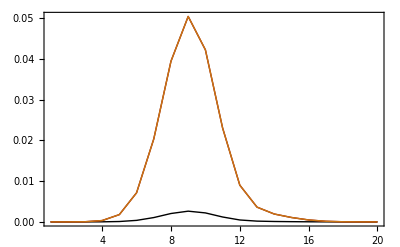

{{1.,-7.51774×10^-7,-7.51774×10^-7},{-1.09234×10^-6,1.,-3.26853×10^-6},{-1.09234×10^-6,4.36087×10^-6,1.}}

```mathematica
means=Map[Total,(alpha.vTilde).DiagonalMatrix[pi*posi]]/Map[Total,(alpha.vTilde).DiagonalMatrix[pi]]//Simplify;variances=Map[Total,(alpha.vTilde).DiagonalMatrix[pi*posi^2]]/Map[Total,(alpha.vTilde).DiagonalMatrix[pi]]//Simplify;
evals=Op["Eigenvalues"]@listOfEstimations[[fiberNo,index]];
error=variances-means^2;
minimizer=Total[error];
minimizer=-Tr[(Inverse[Transpose[alpha]].DiagonalMatrix[Join[{1},evals]].Transpose[alpha])-IdentityMatrix[3]];
minimizer=-Total@Flatten@Log[(alpha.vTilde).DiagonalMatrix[pi].Transpose[(alpha.vTilde)]//Simplify]//Simplify;
minimizer=Total@Flatten@Chop[DiagonalMatrix[1/alpha[[All,1]]^2].(alpha^2)//FullSimplify]//FullSimplify;
constr=Flatten@Map[Thread,Thread[alpha.vTilde>0]];
If[True,constr=Join[constr,{a21>0.01,a31>0.01,a21+a31<0.99}]];
erg=FindMinimum[{minimizer,constr},{a21,a22,a23,a31,a32,a33},MaxIterations->2000];
alphaEst=alpha/.erg[[2]]
(variances)/.erg[[2]]
means/.erg[[2]]
DiagonalMatrix[1/alpha[[All,1]]].(alpha^2)/.erg[[2]]
ListPlot[DiagonalMatrix[alpha[[All,1]]].(alpha.vTilde).DiagonalMatrix[pi]/.erg[[2]],PlotRange->All]
Inverse[Transpose[alpha]].Transpose[alpha]/.erg[[2]]
```

```mathematica
pi=-mixinList[[index,1,All,1]]
```

{5.0388×10^-7,0.0000156355,0.00019162,0.00163837,0.00889968,0.0355359,0.101236,0.196092,0.250687,0.209961,0.114622,0.0448316,0.0180073,0.00962436,0.00538574,0.00237131,0.000746745,0.000172486,0.0000233473,2.96585×10^-6}

```mathematica
ListPlot[DiagonalMatrix[alpha[[All,1]]].(alpha.vTilde).DiagonalMatrix[pi]/.erg[[2]],PlotRange->All]
```

ReplaceAll::reps: {a21, a22, a23, a31, a32, a33} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

NMinimize::nnum: The function value 3 - 3\ ({{0.628669, 1.39889, -1.02756}, {0.0677419, 0.721782, 0.210476}, {0.0485946, -0.148144, 1.09955}}/. {0.518725, 0.0591062, -0.115551, 0.341901, -0.0621655, 0.0879203}) is not a number at {a21, a22, a23, a31, a32, a33} = {0.518725, 0.0591062, -0.115551, 0.341901, -0.0621655, 0.0879203}.

ListPlot::lpn: {« 1 »}/. {a21, a22, a23, a31, a32, a33} is not a list of numbers or pairs of numbers.

ListPlot[{{0.+5.0388×10^-7 (0.+(1.-a21-a31) (1. (1.-a21-a31)-1.51523 (-a22-a32)+0.117785 (-a23-a33))),0.+0.0000156355 (0.+(1.-a21-a31) (1. (1.-a21-a31)-1.51831 (-a22-a32)+0.143497 (-a23-a33))),0.+0.00019162 (0.+(1.-a21-a31) (1. (1.-a21-a31)-1.51604 (-a22-a32)+0.130686 (-a23-a33))),0.+0.00163837 (0.+(1.-a21-a31) (1. (1.-a21-a31)-1.48633 (-a22-a32)+0.133117 (-a23-a33))),0.+0.00889968 (0.+(1.-a21-a31) (1. (1.-a21-a31)-1.23914 (-a22-a32)-0.0208281 (-a23-a33))),0.+0.0355359 (0.+(1.-a21-a31) (1. (1.-a21-a31)-0.92749 (-a22-a32)-0.122173 (-a23-a33))),0.+0.101236 (0.+(1.-a21-a31) (1. (1.-a21-a31)-0.63132 (-a22-a32)-0.220233 (-a23-a33))),0.+0.196092 (0.+(1.-a21-a31) (1. (1.-a21-a31)-0.305976 (-a22-a32)-0.271647 (-a23-a33))),0.+0.250687 (0.+(1.-a21-a31) (1. (1.-a21-a31)+0.0163683 (-a22-a32)-0.265657 (-a23-a33))),0.+0.209961 (0.+(1.-a21-a31) (1. (1.-a21-a31)+0.313649 (-a22-a32)-0.160099 (-a23-a33))),0.+0.114622 (0.+(1.-a21-a31) (1. (1.-a21-a31)+0.564462 (-a22-a32)+0.163615 (-a23-a33))),0.+0.0448316 (0.+(1.-a21-a31) (1. (1.-a21-a31)+0.641862 (-a22-a32)+0.973274 (-a23-a33))),0.+0.0180073 (0.+(1.-a21-a31) (1. (1.-a21-a31)+0.365139 (-a22-a32)+2.51564 (-a23-a33))),0.+0.00962436 (0.+(1.-a21-a31) (1. (1.-a21-a31)+0.0957214 (-a22-a32)+3.55772 (-a23-a33))),0.+0.00538574 (0.+(1.-a21-a31) (1. (1.-a21-a31)+0.0425647 (-a22-a32)+3.93456 (-a23-a33))),0.+0.00237131 (0.+(1.-a21-a31) (1. (1.-a21-a31)+0.0607509 (-a22-a32)+4.0286 (-a23-a33))),0.+0.000746745 (0.+(1.-a21-a31) (1. (1.-a21-a31)+0.0824673 (-a22-a32)+4.04647 (-a23-a33))),0.+0.000172486 (0.+(1.-a21-a31) (1. (1.-a21-a31)+0.0949869 (-a22-a32)+4.05539 (-a23-a33))),0.+0.0000233473 (0.+(1.-a21-a31) (1. (1.-a21-a31)+0.088928 (-a22-a32)+4.06524 (-a23-a33))),0.+2.96585×10^-6 (0.+(1.-a21-a31) (1. (1.-a21-a31)+0.0874073 (-a22-a32)+4.06306 (-a23-a33)))},{0.+5.0388×10^-7 (0.+a21 (1. a21-1.51523 a22+0.117785 a23)),0.+0.0000156355 (0.+a21 (1. a21-1.51831 a22+0.143497 a23)),0.+0.00019162 (0.+a21 (1. a21-1.51604 a22+0.130686 a23)),0.+0.00163837 (0.+a21 (1. a21-1.48633 a22+0.133117 a23)),0.+0.00889968 (0.+a21 (1. a21-1.23914 a22-0.0208281 a23)),0.+0.0355359 (0.+a21 (1. a21-0.92749 a22-0.122173 a23)),0.+0.101236 (0.+a21 (1. a21-0.63132 a22-0.220233 a23)),0.+0.196092 (0.+a21 (1. a21-0.305976 a22-0.271647 a23)),0.+0.250687 (0.+a21 (1. a21+0.0163683 a22-0.265657 a23)),0.+0.209961 (0.+a21 (1. a21+0.313649 a22-0.160099 a23)),0.+0.114622 (0.+a21 (1. a21+0.564462 a22+0.163615 a23)),0.+0.0448316 (0.+a21 (1. a21+0.641862 a22+0.973274 a23)),0.+0.0180073 (0.+a21 (1. a21+0.365139 a22+2.51564 a23)),0.+0.00962436 (0.+a21 (1. a21+0.0957214 a22+3.55772 a23)),0.+0.00538574 (0.+a21 (1. a21+0.0425647 a22+3.93456 a23)),0.+0.00237131 (0.+a21 (1. a21+0.0607509 a22+4.0286 a23)),0.+0.000746745 (0.+a21 (1. a21+0.0824673 a22+4.04647 a23)),0.+0.000172486 (0.+a21 (1. a21+0.0949869 a22+4.05539 a23)),0.+0.0000233473 (0.+a21 (1. a21+0.088928 a22+4.06524 a23)),0.+2.96585×10^-6 (0.+a21 (1. a21+0.0874073 a22+4.06306 a23))},{0.+5.0388×10^-7 (0.+a31 (1. a31-1.51523 a32+0.117785 a33)),0.+0.0000156355 (0.+a31 (1. a31-1.51831 a32+0.143497 a33)),0.+0.00019162 (0.+a31 (1. a31-1.51604 a32+0.130686 a33)),0.+0.00163837 (0.+a31 (1. a31-1.48633 a32+0.133117 a33)),0.+0.00889968 (0.+a31 (1. a31-1.23914 a32-0.0208281 a33)),0.+0.0355359 (0.+a31 (1. a31-0.92749 a32-0.122173 a33)),0.+0.101236 (0.+a31 (1. a31-0.63132 a32-0.220233 a33)),0.+0.196092 (0.+a31 (1. a31-0.305976 a32-0.271647 a33)),0.+0.250687 (0.+a31 (1. a31+0.0163683 a32-0.265657 a33)),0.+0.209961 (0.+a31 (1. a31+0.313649 a32-0.160099 a33)),0.+0.114622 (0.+a31 (1. a31+0.564462 a32+0.163615 a33)),0.+0.0448316 (0.+a31 (1. a31+0.641862 a32+0.973274 a33)),0.+0.0180073 (0.+a31 (1. a31+0.365139 a32+2.51564 a33)),0.+0.00962436 (0.+a31 (1. a31+0.0957214 a32+3.55772 a33)),0.+0.00538574 (0.+a31 (1. a31+0.0425647 a32+3.93456 a33)),0.+0.00237131 (0.+a31 (1. a31+0.0607509 a32+4.0286 a33)),0.+0.000746745 (0.+a31 (1. a31+0.0824673 a32+4.04647 a33)),0.+0.000172486 (0.+a31 (1. a31+0.0949869 a32+4.05539 a33)),0.+0.0000233473 (0.+a31 (1. a31+0.088928 a32+4.06524 a33)),0.+2.96585×10^-6 (0.+a31 (1. a31+0.0874073 a32+4.06306 a33))}}/.{a21,a22,a23,a31,a32,a33},PlotRange→All]

0.55

```mathematica
proj=1/20*alpha.vTilde/.erg[[2]]
```

{{0.0475068,0.0474763,0.0474765,0.0468562,0.0423321,0.0362898,0.0305539,0.0240474,0.0173931,0.010891,0.00454848,-8.72293×10^-10,0.0000628096,0.00180179,0.00151976,0.00080223,0.000290161,1.13742×10^-9,0.0000887037,0.00012797},{0.00223891,0.00252366,0.00238309,0.00246353,0.00116669,0.000578608,-1.14879×10^-9,7.22108×10^-9,0.000642659,0.00236459,0.00646628,0.0157442,0.0326617,0.0439446,0.0481037,0.0491978,0.0494382,0.0495613,0.0496616,0.0496343},{0.000254282,2.36412×10^-10,0.000140459,0.000680225,0.00650119,0.0131316,0.0194461,0.0259526,0.0319643,0.0367444,0.0389852,0.0342558,0.0172755,0.00425358,0.000376531,-1.50629×10^-9,0.000271607,0.000438749,0.000249656,0.000237766}}

```mathematica
clF[M_]:=proj.M.Transpose[proj];
tlF[M_]:=Inverse[proj.Transpose[proj]].proj.M.Transpose[proj];
```

```mathematica
Map[#/Total[#]&,#]&[clF[listOfListOfCM[[fiberNo,7,1,1]]]]//MatrixForm
```

(0.392799 | 0.0320061 | 0.575195
0.0782801 | 0.360761 | 0.560959
0.24441 | 0.097438 | 0.658152)

```mathematica
tlF[listOfListOfCM[[fiberNo,7,1,1]]]/100000
```

{{0.189343,-0.122516,-0.257687},{-0.135853,0.0996882,-0.202995},{1.66952,0.719402,4.81815}}

```mathematica
Map[Total,(alpha.vTilde).DiagonalMatrix[posi*pi]]/alpha[[All,1]]
```

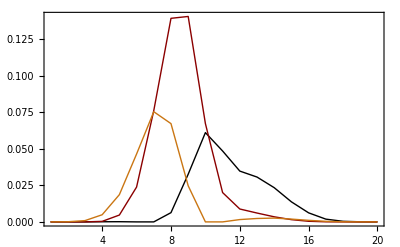

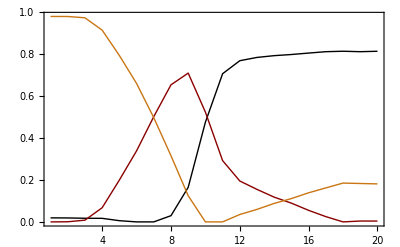

```mathematica
ListPlot[alphaEst.vTilde.DiagonalMatrix[-mixinList[[index,1,All,1]]],PlotRange->All]
ListPlot[alphaEst.vTilde,PlotRange->All]
```

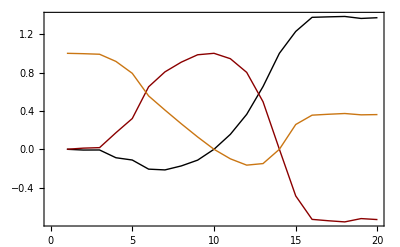

```mathematica
ListPlot[PCCAAlgorithm[estRightEV[[7]],3][[2,1]]]
```

```mathematica
DiagonalMatrix[1/Diagonal[vTilde.mQ]].vTilde.mQ
```

{{1.,-0.00839134,0.00378405},{0.0157975,1.,0.198919},{-0.408221,0.705421,1.}}

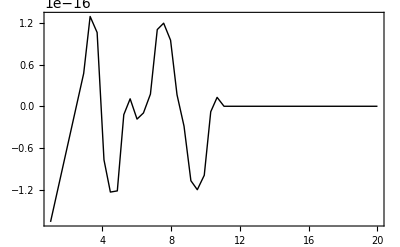

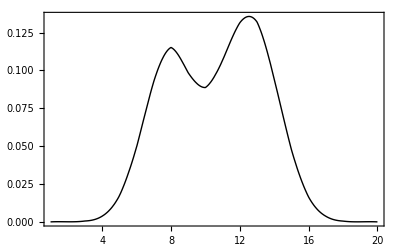

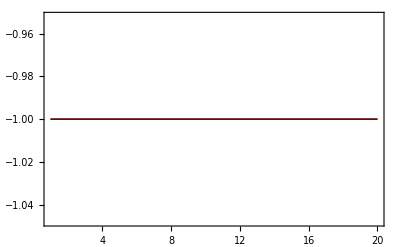

```mathematica
Plot[hh[z],{z,1,20}]
Plot[piF[z],{z,1,20}]
Plot[{ffFix[z],gg[z]},{z,1,20}]
```

```mathematica
nnn=mPiI;
Outer[#1.nnn.#2/Sqrt[(#1.nnn.#1)]/Sqrt[(#2.nnn.#2)]&,Transpose@mQ,Transpose@mQ,1]
```

{{1.,-0.00977901,0.00851418},{-0.00977901,1.,0.37925},{0.00851418,0.37925,1.}}

```mathematica
pi=1/Diagonal[mPiI]
```

{9.25086×10^-6,0.0000768209,0.00058642,0.0037931,0.0172262,0.0493798,0.0927282,0.115192,0.0985041,0.0887459,0.106743,0.131501,0.132011,0.0942989,0.0477206,0.0163906,0.00373028,0.000534233,0.0000521311,7.45922×10^-6}

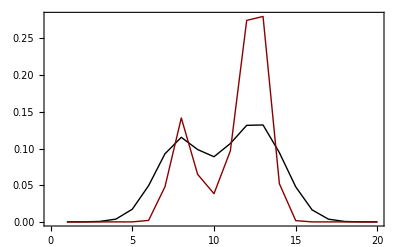

```mathematica
ListPlot[Map[#/Total[#]&,{pi,pi^5}]]
```

```mathematica
Transpose[mQ].mQ
```

{{0.0997622,0.00586888,0.00745868},{0.00586888,0.0708279,0.00918434},{0.00745868,0.00918434,0.0118559}}

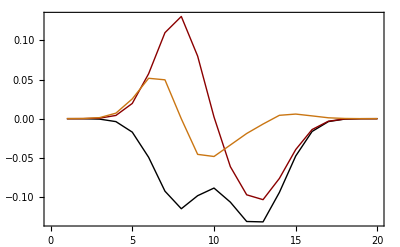

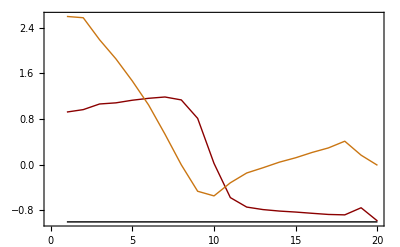

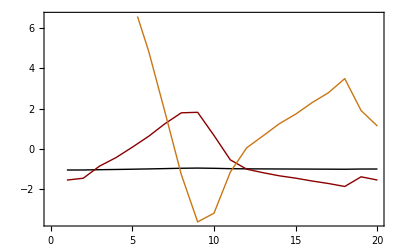

```mathematica
ListPlot[Transpose[mQ]]
ListPlot[Transpose[mW]]
ListPlot[Transpose[mVC]]
```

67.5271

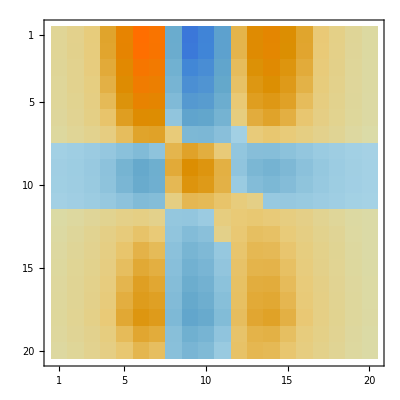

```mathematica
Max[mM]
MatrixPlot[mM]
```

```mathematica
Transpose[(mPiI.mV)].(Transpose[Op["Rejection"]@estim])
```

{{2.17165,-6.09675,-0.354715},{1.10724,-4.43548,-0.898927},{-4.17917,7.91656,0.103516}}

```mathematica
mW
```

{{-0.0000205668,-0.000169646,-0.00130952},{0.0000450475,0.000385516,0.00308517},{0.000232307,0.00190781,0.0122514},{-0.000156958,-0.00213134,-0.0105445},{0.00054897,-0.0101227,-0.0208923},{-0.00534812,0.00729827,-0.00585255},{0.00349494,-0.00617722,-0.0144947},{-0.00410435,0.0201647,-0.0175385},{0.00266578,-0.00816443,0.00589154},{0.00884753,-0.0211403,-0.139264},{0.00290189,-0.00358315,-0.0369731},{-0.01133,-0.0243331,0.0601526},{0.00694381,0.0124118,0.29117},{0.00125549,0.0184779,0.122974},{-0.201612,0.315461,-0.311498},{0.0228351,0.635898,0.70796},{0.166583,0.641851,-0.51611},{-0.564768,0.25971,-0.0829883},{-0.593485,-0.112045,0.050188},{0.509475,0.0438097,-0.0202036}}

```mathematica
Max[mM]
```

67.5271

```mathematica
MatrixPlot[mM]
```

-Graphics-

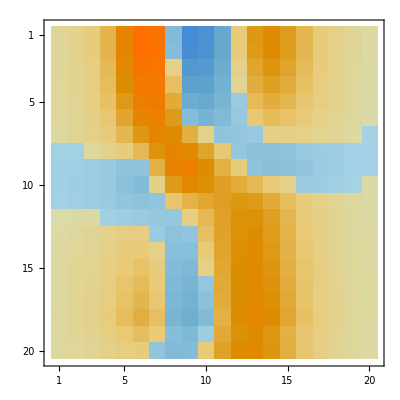

```mathematica
MatrixPlot[mM.mV.mAT.DiagonalMatrix[{1,0.99,0.97}].mA.mVT]
```

```mathematica
Chop@Eigenvalues[mM.mV.mAT.DiagonalMatrix[{1,0.9,0.1}].mA.mVT]
```

{1.,0.9,0.1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

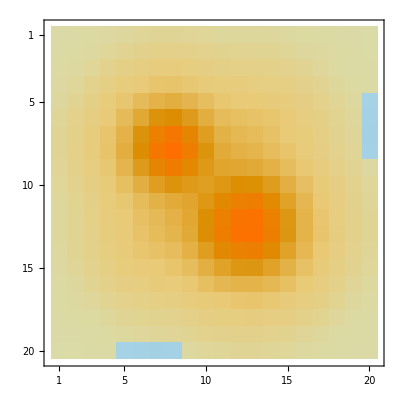

```mathematica
MatrixPlot[mV.Transpose[mA].DiagonalMatrix[{1,0.9,0.1}].mA.Transpose[mV]]
```

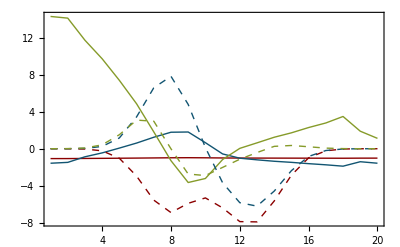

```mathematica
ListPlot[Join[Transpose[mM.mV.mAT],Transpose[mV.mAT]*60],PlotRange->All,PlotStyle->ToPlotStyle[{2,5,4,2,5,4},{Solid,Solid,Solid,Dashed,Dashed,Dashed}]]
```

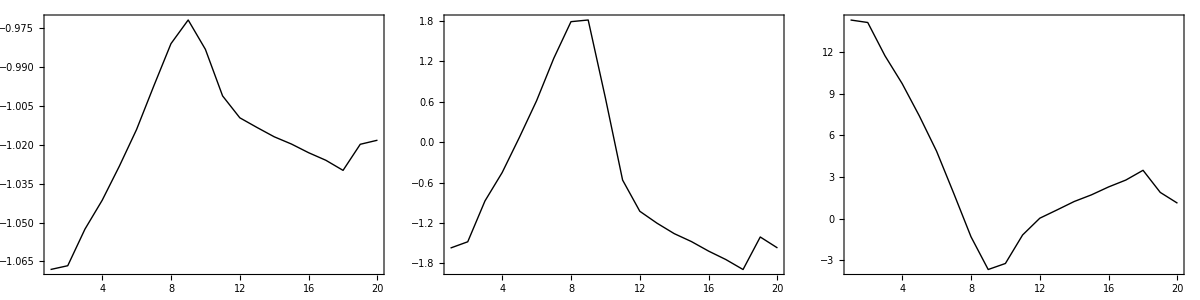

```mathematica
Grid[Partition[Table[ListPlot[Transpose[mM.mV.mAT][[nn]],PlotRange->All],{nn,3}],3]]
```

```mathematica
Block[{nn=9},
f=BSplineFunction[(MapIndexed[#*orientVec[[All,nn]]*1/(Abs@evList[[nn,1,#2[[1]],2]])^(0.5)&,Transpose@evList[[nn,{mixVec[[nn]],5-mixVec[[nn]]},All,2]]])];
p=Interpolation[Transpose[{Range[0,1,1/(Length@evList[[7,1,All,2]]-1)],5*Abs@evList[[nn,1,All,2]]}]];
]
ParametricPlot[f[x],{x,0,1},PlotRange->{{-1,1},{-1,1}}*0.5,Frame->True,Axes->False,ColorFunction->(ColorData["TemperatureMap"][p[#3]/2+0.5]&),ColorFunctionScaling->True]//thick$color[2(Abs[#3])&]
```

Function::slotn: Slot number 3 in 2\ Abs[#3] & cannot be filled from (2\ Abs[#3] &)[0.000974005, -0.00114803].

Function::slotn: Slot number 3 in 2\ Abs[#3] & cannot be filled from (2\ Abs[#3] &)[0.000890945, -0.00124565].

Function::slotn: Slot number 3 in 2\ Abs[#3] & cannot be filled from (2\ Abs[#3] &)[0.000768533, -0.00139279].

General::stop: Further output of Function :: slotn will be suppressed during this calculation.

```mathematica
BSplineFunction
```

```mathematica
Graphics[
Table[
BSplineCurve[(MapIndexed[#*orientVec[[All,nn]]*1/(Abs@evList[[nn,1,#2[[1]],2]])^(0.85)&,Transpose@evList[[nn,{mixVec[[nn]],5-mixVec[[nn]]},All,2]]])]
,{nn,{12}}
],PlotRange->{{-1,1},{-1,1}}*1]
```

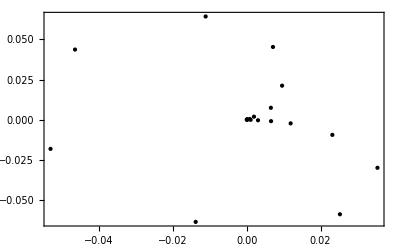
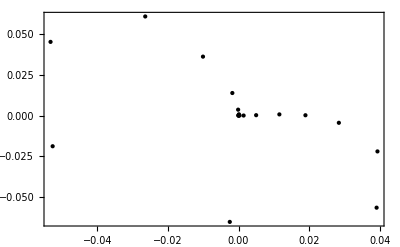
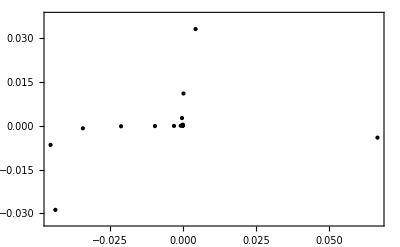
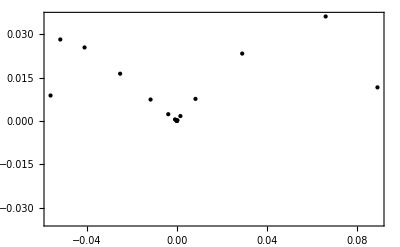
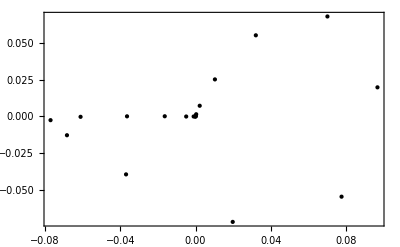
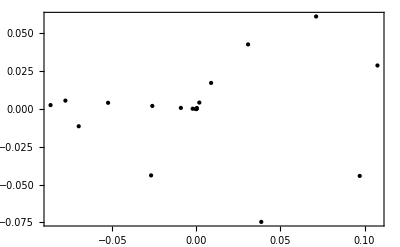
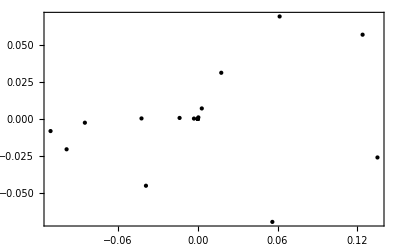
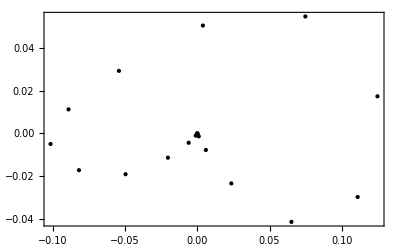

```mathematica
Table[
ListPlot[Transpose@evList[[nn,{If[ev==1,mixVec[[nn]],5-mixVec[[nn]]],If[ev≠1,mixVec[[nn]],5-mixVec[[nn]]]},All,2]],Joined->False]
,{ev,1,1}
,{nn,prange}
]
```

```mathematica
VV[var_,st_?ListQ,opts___]:=Module[{size},size=Padding/.{opts}/.{Padding->2};
ToExpression[ToString[var]<>StringJoin[Map[PadInteger[#,size]&,st]]]]
selModel[ii_,jj_]:=Thread[Flatten@sM->UnitVector[size^2,(ii-1)*size+jj]]
```

```mathematica
evs=evList[[1,All,All,2]];
evs=DiagonalMatrix[{-1,1,1}].evs;
tss=
```

```mathematica
evList
```

```mathematica
bM=Transpose@{
{1-a0102-a0103,a0102,a0103},
{a0201,a0202,a0203},
{a0301,a0302,a0303}
};
```

```mathematica
model=Total@Flatten[DiagonalMatrix[1/bM[[All,1]]].(bM^2)]
```

1+a0201^2/(1-a0102-a0103)+a0202^2/a0102+a0203^2/a0103+a0301^2/(1-a0102-a0103)+a0302^2/a0102+a0303^2/a0103

```mathematica
model/.rule
```

1.32667

```mathematica
DiagonalMatrix[1/bM[[All,1]]].Transpose@(bM^2)
```

{{1-a0102-a0103,a0102^2/(1-a0102-a0103),a0103^2/(1-a0102-a0103)},{0,a0202^2/a0102,a0203^2/a0102},{0,a0302^2/a0103,a0303^2/a0103}}

```mathematica
evs
```

{{4.27055×10^-6,0.0000326028,0.000234146,0.00099729,0.00295964,0.00657798,0.0109405,0.0183612,0.0376286,0.0807388,0.144001,0.201851,0.209115,0.158824,0.0854658,0.0322901,0.00817468,0.00130965,0.000143157,0.0000118013},{1.00032×10^-6,0.0000197482,0.000099686,0.000465998,0.00135559,0.00354566,0.00718977,0.0135562,0.0241666,0.039725,0.0443259,0.0217252,-0.0215917,-0.05211,-0.0495592,-0.0268613,-0.0083081,-0.00138725,-0.000181796,-2.24925×10^-6},{-0.0000231478,-0.000163559,-0.00123128,-0.00563354,-0.0163187,-0.0329802,-0.0432773,-0.0358304,-0.015043,0.00887968,0.0279136,0.0378843,0.0363029,0.0245587,0.00993526,0.00195877,0.000197898,0.0000367114,-0.0000186624,-1.17068×10^-6}}

```mathematica
rule=Thread[Flatten[aM]->{0.2,0.3,0.5,0,0,0,0,0,0}];
```

```mathematica
rule=Thread[Flatten[aM]->{0.2,0.3,0.5,0,0.1,-0.2,0,0.2,-0.2}];
```

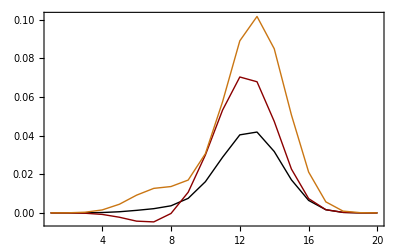

```mathematica
ListPlot[bM.evs/.rule,PlotRange->All]
```

```mathematica
Block[
{states=3},
aM=Table[VV[a,{i,j}],{i,states},{j,states}]
]
```

{{a0101,a0102,a0103},{a0201,a0202,a0203},{a0301,a0302,a0303}}

```mathematica
lV=Table[VV[l,{i}],{i,states-1}];
lD=DiagonalMatrix[Join[{1},Exp[-t*lV]]];
sM=Table[VV[s,{i,j}],{i,rrange},{j,rrange}];
model=Total@Flatten[sM*qM.lD.Transpose@qM];
constraints=Thread[lV≥0];
corMList=Map[Chop[Transpose[pro].(ToCorrelationMatrix@#)[[1]].pro]&,listOfCM];
data=Flatten[Table[Transpose[Join[{trange},Transpose[{UnitVector[states^2,(i-1)*states+j]}].{trange*0+1},{corMList[[trange,rrange[[i]],rrange[[j]]]]}]],{i,states},{j,states}],2];
data//Dimensions;
vars=Join[{t},Flatten[sM]];
params=Join[Flatten[Transpose[{qM,IdentityMatrix[states]},{3,1,2}],{1,2}],Flatten[Transpose[{lV,lI}],{1}]];
useConstraints=UseConstraints/.{opts}/.{UseConstraints->False};
If[useConstraints,
result=FindFit[data,{model,constraints},params,vars,MaxIterations->2000];
```

```mathematica
evs=evList[[9,All,All,2]];
evs=DiagonalMatrix[{-1,1,1}].evs;
```

```mathematica
evals=Op["Eigenvalues"]@listOfEstimations[[1,1]];
```

```mathematica
Total@Flatten@(Transpose@evs.DiagonalMatrix[Join[{1},evals]].evs)
```

1.00011

```mathematica
evs.DiagonalMatrix[evs[[1]]].Transpose[evs]
```

{{0.0352363,-0.00106643,0.0075967},{-0.00106643,0.00259164,0.000443867},{0.0075967,0.000443867,0.00213301}}

```mathematica
mM=evs.Transpose[evs]
mW=evs.DiagonalMatrix[evs[[1]]].Transpose[evs]
```

{{0.172574,-0.00418178,0.0312207},{-0.00418178,0.0183098,0.00508383},{0.0312207,0.00508383,0.0149479}}

{{0.0352363,-0.00106643,0.0075967},{-0.00106643,0.00259164,0.000443867},{0.0075967,0.000443867,0.00213301}}

```mathematica
(DiagonalMatrix@(1/bM.mM[[1]])//Chop).(bM.mW.Transpose[bM])/.rule
Total@Flatten@%
```

{{0.0347697,0.0577876,0.0816618},{0.0351146,0.05872,0.0818362},{0.0345503,0.0569806,0.0819661}}

0.523387

```mathematica
Total@Map[Total,bM.evs]//Simplify
```

1.00005-0.000697479 a0201-0.000697479 a0202-0.000697479 a0203+0.00339973 a0301+0.00339973 a0302+0.00339973 a0303

```mathematica
Map[Total,evs]
```

{1.00005,-0.000697479,0.00339973}

```mathematica
Total@Map[Total,bM.evs]//Simplify
```

1.00005-0.000697479 a0201-0.000697479 a0202-0.000697479 a0203+0.00339973 a0301+0.00339973 a0302+0.00339973 a0303

```mathematica
bM
```

{{1-a0102-a0103,a0201,a0301},{a0102,a0202,a0302},{a0103,a0203,a0303}}

```mathematica
aM
```

{{a0101,a0102,a0103},{a0201,a0202,a0203},{a0301,a0302,a0303}}

```mathematica
evs.Transpose[evs]
```

{{0.172574,-0.00418178,0.0312207},{-0.00418178,0.0183098,0.00508383},{0.0312207,0.00508383,0.0149479}}

```mathematica
aM.mM[[1]]
```

{0.147294 a0101-0.00272393 a0102+0.022821 a0103,0.147294 a0201-0.00272393 a0202+0.022821 a0203,0.147294 a0301-0.00272393 a0302+0.022821 a0303}

```mathematica
Map[Total,(DiagonalMatrix@(1/mM[[1]])//Chop).(mW)/.rule]
```

{0.20016,-0.250739,0.228101}

```mathematica
Map[Total,(DiagonalMatrix@(1/bM.mM[[1]])//Chop).(bM.mW.Transpose[bM])/.rule]
```

{0.204799,0.208007,0.203095}

```mathematica
mM[[1]]
```

{0.172574,-0.00418178,0.0312207}

```mathematica
Total@Map[Total,bM.evs]/.rule
```

1.00012

```mathematica
const=Join[Thread[{1-a0102-a0103,a0102,a0103}>0.1],Flatten@Map[Thread,Thread[bM.evs≥0]],Flatten@Map[Thread,Thread[bM.evs≤1]]];
```

```mathematica
vars=Drop[Flatten@aM,1];
```

```mathematica
mW=evs.DiagonalMatrix[1/evs[[1]]].Transpose[evs];
```

```mathematica
model2=Total@Flatten[(1-IdentityMatrix[3])*(bM.mW.Transpose[bM])^2];
```

```mathematica
model=-Total@Diagonal[(bM.mW.Transpose[bM])];
```

```mathematica
model1=a0102^2+a0103^2+(1-a0102-a0103)^2;
```

```mathematica
model=Total@Map[Max,bM.evs]
```

```mathematica
Apply[And,const]//Reduce
```

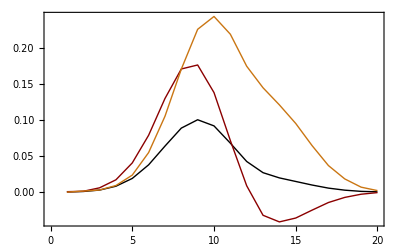

```mathematica
ListPlot[(bM.evs.DiagonalMatrix[1/Sqrt[evs[[1]]]]//Simplify//Chop)/.rule]
```

```mathematica
Reduce
```

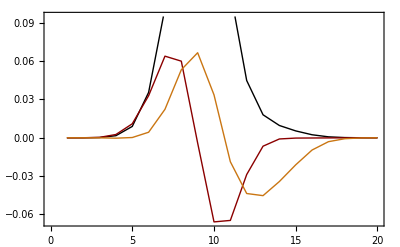

```mathematica
ListPlot@evs
```

```mathematica
pcca=FindMinimum[{model,const},{{a0102,0.1},{a0103,0.1},a0201,a0202,a0203,a0301,a0302,a0303},MaxIterations->200];
```

FindMinimum::eit: The algorithm does not converge to the tolerance of 4.80622×10^-6 in 200 iterations. The best estimated solution, with feasibility residual, KKT residual, or complementary residual of {0.0000665659, 0.0507884, 5.42901×10^-7}, is returned.

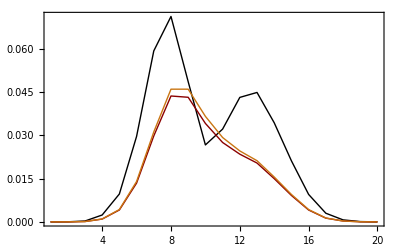

```mathematica
ListPlot[bM.evs/.pcca[[2]],PlotRange->All]
```

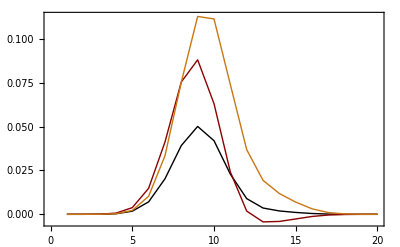

```mathematica
ListPlot[bM.evs/.rule]
```

```mathematica
evs.(PseudoInverse@evs)
```

{{1.,-6.22671×10^-17,4.61109×10^-17},{-3.8935×10^-17,1.,2.00982×10^-17},{-4.61905×10^-17,4.6319×10^-17,1.}}

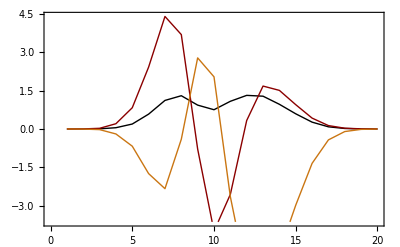

```mathematica
ListPlot@Transpose[PseudoInverse@evs]
```

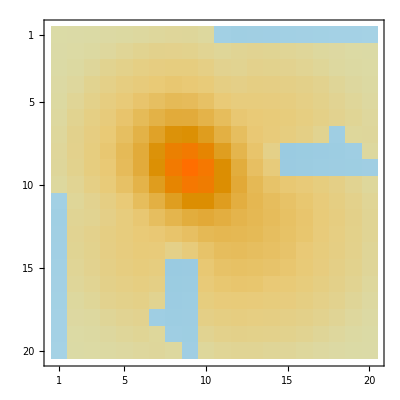

```mathematica
MatrixPlot[Transpose[evs].evs]
```

```mathematica
chiQ=Map[#/evs[[1]]&,evs];
```

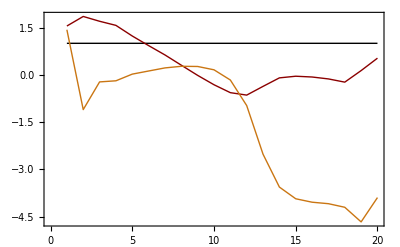

```mathematica
ListPlot[Map[#/evs[[1]]&,evs]]
```

```mathematica
aM.evs
```

{{5.0388×10^-7 a0101+7.80324×10^-7 a0102+7.21045×10^-7 a0103,0.0000156355 a0101+0.0000289495 a0102-0.0000172274 a0103,0.00019162 a0101+0.000325585 a0102-0.0000428398 a0103,0.00163837 a0101+0.0025704 a0102-0.000308448 a0103,0.00889968 a0101+0.0109613 a0102+0.000207025 a0103,0.0355359 a0101+0.0329592 a0102+0.00434155 a0103,0.101236 a0101+0.0639125 a0102+0.0222956 a0103,0.196092 a0101+0.0599996 a0102+0.0532679 a0103,0.250687 a0101-0.00410332 a0102+0.0665968 a0103,0.209961 a0101-0.0658541 a0102+0.0336145 a0103,0.114622 a0101-0.0647001 a0102-0.018754 a0103,0.0448316 a0101-0.0287757 a0102-0.0436335 a0103,0.0180073 a0101-0.00657518 a0102-0.0453 a0103,0.00962436 a0101-0.000921257 a0102-0.0342408 a0103,0.00538574 a0101-0.000233369 a0102-0.0211587 a0103,0.00237131 a0101-0.000161433 a0102-0.00957412 a0103,0.000746745 a0101-0.0000962502 a0102-0.00305031 a0103,0.000172486 a0101-0.00003981 a0102-0.000724138 a0103,0.0000233473 a0101+3.15483×10^-6 a0102-0.000108843 a0103,2.96585×10^-6 a0101+1.56993×10^-6 a0102-0.0000115401 a0103},{5.0388×10^-7 a0201+7.80324×10^-7 a0202+7.21045×10^-7 a0203,0.0000156355 a0201+0.0000289495 a0202-0.0000172274 a0203,0.00019162 a0201+0.000325585 a0202-0.0000428398 a0203,0.00163837 a0201+0.0025704 a0202-0.000308448 a0203,0.00889968 a0201+0.0109613 a0202+0.000207025 a0203,0.0355359 a0201+0.0329592 a0202+0.00434155 a0203,0.101236 a0201+0.0639125 a0202+0.0222956 a0203,0.196092 a0201+0.0599996 a0202+0.0532679 a0203,0.250687 a0201-0.00410332 a0202+0.0665968 a0203,0.209961 a0201-0.0658541 a0202+0.0336145 a0203,0.114622 a0201-0.0647001 a0202-0.018754 a0203,0.0448316 a0201-0.0287757 a0202-0.0436335 a0203,0.0180073 a0201-0.00657518 a0202-0.0453 a0203,0.00962436 a0201-0.000921257 a0202-0.0342408 a0203,0.00538574 a0201-0.000233369 a0202-0.0211587 a0203,0.00237131 a0201-0.000161433 a0202-0.00957412 a0203,0.000746745 a0201-0.0000962502 a0202-0.00305031 a0203,0.000172486 a0201-0.00003981 a0202-0.000724138 a0203,0.0000233473 a0201+3.15483×10^-6 a0202-0.000108843 a0203,2.96585×10^-6 a0201+1.56993×10^-6 a0202-0.0000115401 a0203},{5.0388×10^-7 a0301+7.80324×10^-7 a0302+7.21045×10^-7 a0303,0.0000156355 a0301+0.0000289495 a0302-0.0000172274 a0303,0.00019162 a0301+0.000325585 a0302-0.0000428398 a0303,0.00163837 a0301+0.0025704 a0302-0.000308448 a0303,0.00889968 a0301+0.0109613 a0302+0.000207025 a0303,0.0355359 a0301+0.0329592 a0302+0.00434155 a0303,0.101236 a0301+0.0639125 a0302+0.0222956 a0303,0.196092 a0301+0.0599996 a0302+0.0532679 a0303,0.250687 a0301-0.00410332 a0302+0.0665968 a0303,0.209961 a0301-0.0658541 a0302+0.0336145 a0303,0.114622 a0301-0.0647001 a0302-0.018754 a0303,0.0448316 a0301-0.0287757 a0302-0.0436335 a0303,0.0180073 a0301-0.00657518 a0302-0.0453 a0303,0.00962436 a0301-0.000921257 a0302-0.0342408 a0303,0.00538574 a0301-0.000233369 a0302-0.0211587 a0303,0.00237131 a0301-0.000161433 a0302-0.00957412 a0303,0.000746745 a0301-0.0000962502 a0302-0.00305031 a0303,0.000172486 a0301-0.00003981 a0302-0.000724138 a0303,0.0000233473 a0301+3.15483×10^-6 a0302-0.000108843 a0303,2.96585×10^-6 a0301+1.56993×10^-6 a0302-0.0000115401 a0303}}

```mathematica
mM=chiQ.Transpose[chiQ]
mW=chiQ.DiagonalMatrix[evs[[1]]].Transpose[chiQ]
```

{{20.,7.96073,-31.0319},{7.96073,15.3907,1.03751},{-31.0319,1.03751,126.461}}

{{1.00005,-0.000697479,0.00339973},{-0.000697479,0.185664,0.0829544},{0.00339973,0.0829544,0.462223}}

```mathematica
xM1=DiagonalMatrix[#&[(bM.chiQ.evs[[1]])//Chop]]
xM2=(bM.mW.Transpose[bM])//Chop
```

{{0.0000233473 (1. (1-a0102-a0103)+0.135126 a0201-4.66189 a0301)+0.000172486 (1. (1-a0102-a0103)-0.230802 a0201-4.19825 a0301)+0.000746745 (1. (1-a0102-a0103)-0.128893 a0201-4.0848 a0301)+0.00237131 (1. (1-a0102-a0103)-0.0680774 a0201-4.03748 a0301)+0.00538574 (1. (1-a0102-a0103)-0.0433308 a0201-3.92865 a0301)+2.96585×10^-6 (1. (1-a0102-a0103)+0.529335 a0201-3.89101 a0301)+0.00962436 (1. (1-a0102-a0103)-0.0957214 a0201-3.55772 a0301)+0.0180073 (1. (1-a0102-a0103)-0.365139 a0201-2.51564 a0301)+0.0000156355 (1. (1-a0102-a0103)+1.85152 a0201-1.10181 a0301)+0.0448316 (1. (1-a0102-a0103)-0.641862 a0201-0.973274 a0301)+0.00019162 (1. (1-a0102-a0103)+1.69911 a0201-0.223566 a0301)+0.00163837 (1. (1-a0102-a0103)+1.56887 a0201-0.188265 a0301)+0.114622 (1. (1-a0102-a0103)-0.564462 a0201-0.163615 a0301)+0.00889968 (1. (1-a0102-a0103)+1.23165 a0201+0.023262 a0301)+0.0355359 (1. (1-a0102-a0103)+0.92749 a0201+0.122173 a0301)+0.209961 (1. (1-a0102-a0103)-0.313649 a0201+0.160099 a0301)+0.101236 (1. (1-a0102-a0103)+0.63132 a0201+0.220233 a0301)+0.250687 (1. (1-a0102-a0103)-0.0163683 a0201+0.265657 a0301)+0.196092 (1. (1-a0102-a0103)+0.305976 a0201+0.271647 a0301)+5.0388×10^-7 (1. (1-a0102-a0103)+1.54863 a0201+1.43098 a0301),0.,0.},{0.,0.0000233473 (1. a0102+0.135126 a0202-4.66189 a0302)+0.000172486 (1. a0102-0.230802 a0202-4.19825 a0302)+0.000746745 (1. a0102-0.128893 a0202-4.0848 a0302)+0.00237131 (1. a0102-0.0680774 a0202-4.03748 a0302)+0.00538574 (1. a0102-0.0433308 a0202-3.92865 a0302)+2.96585×10^-6 (1. a0102+0.529335 a0202-3.89101 a0302)+0.00962436 (1. a0102-0.0957214 a0202-3.55772 a0302)+0.0180073 (1. a0102-0.365139 a0202-2.51564 a0302)+0.0000156355 (1. a0102+1.85152 a0202-1.10181 a0302)+0.0448316 (1. a0102-0.641862 a0202-0.973274 a0302)+0.00019162 (1. a0102+1.69911 a0202-0.223566 a0302)+0.00163837 (1. a0102+1.56887 a0202-0.188265 a0302)+0.114622 (1. a0102-0.564462 a0202-0.163615 a0302)+0.00889968 (1. a0102+1.23165 a0202+0.023262 a0302)+0.0355359 (1. a0102+0.92749 a0202+0.122173 a0302)+0.209961 (1. a0102-0.313649 a0202+0.160099 a0302)+0.101236 (1. a0102+0.63132 a0202+0.220233 a0302)+0.250687 (1. a0102-0.0163683 a0202+0.265657 a0302)+0.196092 (1. a0102+0.305976 a0202+0.271647 a0302)+5.0388×10^-7 (1. a0102+1.54863 a0202+1.43098 a0302),0.},{0.,0.,0.0000233473 (1. a0103+0.135126 a0203-4.66189 a0303)+0.000172486 (1. a0103-0.230802 a0203-4.19825 a0303)+0.000746745 (1. a0103-0.128893 a0203-4.0848 a0303)+0.00237131 (1. a0103-0.0680774 a0203-4.03748 a0303)+0.00538574 (1. a0103-0.0433308 a0203-3.92865 a0303)+2.96585×10^-6 (1. a0103+0.529335 a0203-3.89101 a0303)+0.00962436 (1. a0103-0.0957214 a0203-3.55772 a0303)+0.0180073 (1. a0103-0.365139 a0203-2.51564 a0303)+0.0000156355 (1. a0103+1.85152 a0203-1.10181 a0303)+0.0448316 (1. a0103-0.641862 a0203-0.973274 a0303)+0.00019162 (1. a0103+1.69911 a0203-0.223566 a0303)+0.00163837 (1. a0103+1.56887 a0203-0.188265 a0303)+0.114622 (1. a0103-0.564462 a0203-0.163615 a0303)+0.00889968 (1. a0103+1.23165 a0203+0.023262 a0303)+0.0355359 (1. a0103+0.92749 a0203+0.122173 a0303)+0.209961 (1. a0103-0.313649 a0203+0.160099 a0303)+0.101236 (1. a0103+0.63132 a0203+0.220233 a0303)+0.250687 (1. a0103-0.0163683 a0203+0.265657 a0303)+0.196092 (1. a0103+0.305976 a0203+0.271647 a0303)+5.0388×10^-7 (1. a0103+1.54863 a0203+1.43098 a0303)}}

{{(1-a0102-a0103) (1.00005 (1-a0102-a0103)-0.000697479 a0201+0.00339973 a0301)+a0201 (-0.000697479 (1-a0102-a0103)+0.185664 a0201+0.0829544 a0301)+(0.00339973 (1-a0102-a0103)+0.0829544 a0201+0.462223 a0301) a0301,a0102 (1.00005 (1-a0102-a0103)-0.000697479 a0201+0.00339973 a0301)+a0202 (-0.000697479 (1-a0102-a0103)+0.185664 a0201+0.0829544 a0301)+(0.00339973 (1-a0102-a0103)+0.0829544 a0201+0.462223 a0301) a0302,a0103 (1.00005 (1-a0102-a0103)-0.000697479 a0201+0.00339973 a0301)+a0203 (-0.000697479 (1-a0102-a0103)+0.185664 a0201+0.0829544 a0301)+(0.00339973 (1-a0102-a0103)+0.0829544 a0201+0.462223 a0301) a0303},{(1-a0102-a0103) (1.00005 a0102-0.000697479 a0202+0.00339973 a0302)+a0201 (-0.000697479 a0102+0.185664 a0202+0.0829544 a0302)+a0301 (0.00339973 a0102+0.0829544 a0202+0.462223 a0302),a0102 (1.00005 a0102-0.000697479 a0202+0.00339973 a0302)+a0202 (-0.000697479 a0102+0.185664 a0202+0.0829544 a0302)+(0.00339973 a0102+0.0829544 a0202+0.462223 a0302) a0302,a0103 (1.00005 a0102-0.000697479 a0202+0.00339973 a0302)+a0203 (-0.000697479 a0102+0.185664 a0202+0.0829544 a0302)+(0.00339973 a0102+0.0829544 a0202+0.462223 a0302) a0303},{(1-a0102-a0103) (1.00005 a0103-0.000697479 a0203+0.00339973 a0303)+a0201 (-0.000697479 a0103+0.185664 a0203+0.0829544 a0303)+a0301 (0.00339973 a0103+0.0829544 a0203+0.462223 a0303),a0102 (1.00005 a0103-0.000697479 a0203+0.00339973 a0303)+a0202 (-0.000697479 a0103+0.185664 a0203+0.0829544 a0303)+a0302 (0.00339973 a0103+0.0829544 a0203+0.462223 a0303),a0103 (1.00005 a0103-0.000697479 a0203+0.00339973 a0303)+a0203 (-0.000697479 a0103+0.185664 a0203+0.0829544 a0303)+(0.00339973 a0103+0.0829544 a0203+0.462223 a0303) a0303}}

```mathematica
xM3=Tr[Inverse[xM1].xM2];
```

```mathematica
Chop[xM3,10^-5]
```

```mathematica
xM3/.rule
```

{{0.2,0.30061,0.49946},{0.2,0.379324,0.409051},{0.2,0.246196,0.56463}}

```mathematica
Map[Total,xM3]
```

{1.00007,0.988375,1.01083}